## Definitions

```mathematica
NbName = "804";Needs["MaTeX`"];
(*Js={0.}; Ks={-1.}; Γs=Table[γ,{γ,0.,.0,.2}]; hV={  {0.10,0,0}  };*)
Ls =Range[40,40,2]; 	    
tV={1};	  
 hV={{0.1,0,0}};
steps=600;
acuracy=6;    
ΔeV=0.099999; eVs=Table[ 1700 ξ, {ξ,0,0,ΔeV} ] ;
ηs=Join[
Table[η+.02,{η,-1.5,0.5,0.1}],
Table[η+.04,{η,-1.5,0.5,0.1}],
Table[η+.06,{η,-1.5,0.5,0.1}],
Table[η+.08,{η,-1.5,0.5,0.1}]
(*,Table[η+.08,{-1.5,0.5,0.1}]*)
];
```

#### Constants

```mathematica
one[i_,j_,N_]:= SparseArray[ {i,j} -> 1, {N,N}];  block[i_,j_] := one[i,j,8];
hc=1/(√3){1,1,1};hb=1/(√2){1,-1,0};ha=1/(√6){1,1,-2};hx={1,0,0};
 hAngle[θ_,ϕ_]:= ha Cos[ϕ π/180] Sin[θ π/180]+hb Sin[ϕ π/180] Sin[θ π/180]+ hc Cos[θ π/180] ;  (* Magnetic field directions a, b, c*)
nx={1/2,(√3)/2};  ny={-1/2,(√3)/2};                                                                                           (* Honeycomb Bravais basis  *)

δx={-√3/2,-1/2}/√3;      δy={√3/2,-1/2}/√3;        δz={0,1}/√3;
```

```mathematica
asites[m_,n_]:=m nx+n ny;
bsites[m_,n_]:=m nx+n ny-δz;
σsites[m_,n_,σ_]:=m nx+n ny-σ δz;
```

```mathematica
Gmat=  {KroneckerProduct[  PauliMatrix[0],-ⅈ PauliMatrix[2] ],KroneckerProduct[- ⅈ PauliMatrix[2],PauliMatrix[3] ],KroneckerProduct[-ⅈ PauliMatrix[2],  PauliMatrix[1] ]};
Mmat=  {KroneckerProduct[  PauliMatrix[3],ⅈ PauliMatrix[2] ],KroneckerProduct[ ⅈ PauliMatrix[2],PauliMatrix[0] ],KroneckerProduct[  PauliMatrix[1],ⅈ PauliMatrix[2] ]};
Nmat=(Mmat-Gmat)/2;
```

```mathematica
toλ[h_,Δv_:0.262]:= {h[[1]]^2,h[[2]]^2,h[[3]]^2}/Δv;
toKappa[h_,Δv_:0.262]:=8h[[1]]h[[2]]h[[3]]/(  3 Δv^2 );
KappaToH[κ_,d_,Δv_:0.262]:=Module[{C=d[[1]]d[[2]]d[[3]]},If[C==0,{0,0,0},  d CubeRoot[3  Δv^2 κ/(8C)]   ]] ;
```

```mathematica
χGx = {{0.5249,0,0,0},{0,-1,0,0},{0,0,0,0},{0,0,0,0}};χGy = {{0.5249,0,0,0},{0,0,0,0},{0,0,-1,0},{0,0,0,0}};χGz ={{0.5249,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1}};
ωGA = ⅈ IdentityMatrix[4]+10^-6 Sum[Mmat[[γ]],{γ,1,3}]; 
ωGB = ωGA;
Uguess=-{χGx,χGy,χGz};
Vguess={ωGA,ωGB};
```

```mathematica
to3digits[list0_]:=Module[{list=list0},If[ Length@list>=3, list, list=Flatten[{{0},list},1]; If[ Length@list>=3, list,  list=Flatten[{{0},list},1] ] ]; StringJoin[ToString/@list]     ];
round[x_]:=N[Round[1000000(x)]/1000000];
```

```mathematica
(* Module[{V=Table[v[[i,j]],{i,1,4},{j,1,4}]  },Table[Tr[V^ᵀ.Nmat[[γ]]],{γ,1,3}]] *)
```

```mathematica
sumtraceG[v_]:=-v⟦1,2⟧-v⟦1,3⟧-v⟦1,4⟧+v⟦2,1⟧-v⟦2,3⟧+v⟦2,4⟧+v⟦3,1⟧+v⟦3,2⟧-v⟦3,4⟧+v⟦4,1⟧-v⟦4,2⟧+v⟦4,3⟧;
traceG[v_]:={-v⟦1,2⟧+v⟦2,1⟧-v⟦3,4⟧+v⟦4,3⟧,-v⟦1,3⟧+v⟦2,4⟧+v⟦3,1⟧-v⟦4,2⟧,-v⟦1,4⟧-v⟦2,3⟧+v⟦3,2⟧+v⟦4,1⟧};
sumtraceM[v_]:=v⟦1,2⟧-v⟦2,1⟧-v⟦3,4⟧+v⟦4,3⟧+v⟦1,3⟧+v⟦2,4⟧-v⟦3,1⟧-v⟦4,2⟧+v⟦1,4⟧-v⟦2,3⟧+v⟦3,2⟧-v⟦4,1⟧;
traceM[v_]:={v⟦1,2⟧-v⟦2,1⟧-v⟦3,4⟧+v⟦4,3⟧,v⟦1,3⟧+v⟦2,4⟧-v⟦3,1⟧-v⟦4,2⟧,v⟦1,4⟧-v⟦2,3⟧+v⟦3,2⟧-v⟦4,1⟧};
sumtraceN[v_]:=v⟦1,2⟧+v⟦1,3⟧+v⟦1,4⟧-v⟦2,1⟧-v⟦3,1⟧-v⟦4,1⟧;
traceN[v_]:={v⟦1,2⟧-v⟦2,1⟧,v⟦1,3⟧-v⟦3,1⟧,v⟦1,4⟧-v⟦4,1⟧};
traceUNUN[u_]:=2{{u⟦1,2⟧ u⟦2,1⟧-u⟦1,1⟧ u⟦2,2⟧,u⟦1,3⟧ u⟦2,1⟧-u⟦1,1⟧ u⟦2,3⟧,u⟦1,4⟧ u⟦2,1⟧-u⟦1,1⟧ u⟦2,4⟧},
{u⟦1,2⟧ u⟦3,1⟧-u⟦1,1⟧ u⟦3,2⟧,u⟦1,3⟧ u⟦3,1⟧-u⟦1,1⟧ u⟦3,3⟧,u⟦1,4⟧ u⟦3,1⟧-u⟦1,1⟧ u⟦3,4⟧},{u⟦1,2⟧ u⟦4,1⟧-u⟦1,1⟧ u⟦4,2⟧,u⟦1,3⟧ u⟦4,1⟧-u⟦1,1⟧ u⟦4,3⟧,u⟦1,4⟧ u⟦4,1⟧-u⟦1,1⟧ u⟦4,4⟧}};
```

```mathematica
(*Module[{V=Table[u[[i,j]],{i,1,4},{j,1,4}]  },Table[Tr[1/2V^ᵀ.Nmat[[α]].V.Nmat[[β]]],{α,1,3},{β,1,3}]] *)
```

```mathematica
(*UpperLeft8x8[matrice_]:={
{0,0,0,0,matrice⟦1,1⟧,matrice⟦1,2⟧,matrice⟦1,3⟧,matrice⟦1,4⟧},{0,0,0,0,matrice⟦2,1⟧,matrice⟦2,2⟧,matrice⟦2,3⟧,matrice⟦2,4⟧},{0,0,0,0,matrice⟦3,1⟧,matrice⟦3,2⟧,matrice⟦3,3⟧,matrice⟦3,4⟧},{0,0,0,0,matrice⟦4,1⟧,matrice⟦4,2⟧,matrice⟦4,3⟧,matrice⟦4,4⟧},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0} };
UpperRight8x8[matrice_]:={
{matrice⟦1,1⟧,matrice⟦1,2⟧,matrice⟦1,3⟧,matrice⟦1,4⟧,0,0,0,0},{matrice⟦2,1⟧,matrice⟦2,2⟧,matrice⟦2,3⟧,matrice⟦2,4⟧,0,0,0,0},{matrice⟦3,1⟧,matrice⟦3,2⟧,matrice⟦3,3⟧,matrice⟦3,4⟧,0,0,0,0},{matrice⟦4,1⟧,matrice⟦4,2⟧,matrice⟦4,3⟧,matrice⟦4,4⟧,0,0,0,0},
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}};
LowerLeft8x8[matrice_]:={
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},
{matrice⟦1,1⟧,matrice⟦1,2⟧,matrice⟦1,3⟧,matrice⟦1,4⟧,0,0,0,0},{matrice⟦2,1⟧,matrice⟦2,2⟧,matrice⟦2,3⟧,matrice⟦2,4⟧,0,0,0,0},{matrice⟦3,1⟧,matrice⟦3,2⟧,matrice⟦3,3⟧,matrice⟦3,4⟧,0,0,0,0},{matrice⟦4,1⟧,matrice⟦4,2⟧,matrice⟦4,3⟧,matrice⟦4,4⟧,0,0,0,0}};
LowerRight8x8[matrice_]:={
{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},
{0,0,0,0,matrice⟦1,1⟧,matrice⟦1,2⟧,matrice⟦1,3⟧,matrice⟦1,4⟧},{0,0,0,0,matrice⟦2,1⟧,matrice⟦2,2⟧,matrice⟦2,3⟧,matrice⟦2,4⟧},{0,0,0,0,matrice⟦3,1⟧,matrice⟦3,2⟧,matrice⟦3,3⟧,matrice⟦3,4⟧},{0,0,0,0,matrice⟦4,1⟧,matrice⟦4,2⟧,matrice⟦4,3⟧,matrice⟦4,4⟧}};*)
```

### Pure Kitaev model definitions

#### file

```mathematica
(*dataToFilePure[ parameters_,L_,acuracy_,gauge_,data_] :=
Module[ {path,f},		createDir@FileNameJoin[  {NotebookDirectory[], "Files","pure", gauge}] ;
		path = toPathPure[parameters,L,acuracy,gauge];		
		f = OpenWrite[path];
		 Write[ f, data];
		 Close[f];                ];
(*toPathPure[κ_,L_,K_,gauge_]:=  
FileNameJoin[  {NotebookDirectory[], "Files","pure", gauge,"data", StringReplace["K=Z-L=Y-kappa=M.txt",     {"Y"-> ToString[L], "M"->  ToString@N[Round[10000κ]/10000]  , "Z"-> ToString[K]}   ] }];*)

toPathPure[parameters0_,L_,acuracy_,gauge_]:= Module[{h ,hS,parameters=parameters0, r,ϕ,θ},h=parameters[[4]] ;hS=parameters[[8]]; {r,θ,ϕ}=hS;   
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
FileNameJoin[{       NotebookDirectory[]   , "Files" ,"pure",gauge,StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],"X4"->  ToString[parameters[[5;;7]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];

loadDataPure[ path_]:= Module[{(*path,*)f,data}, 
(*path= toPathPure[κ,L,K,gauge];*)
f = OpenRead[path];
data=ReadList[ f];
Close[f];
data[[-1]]  ];*)
```

```mathematica
dataToFilePure[ parameters0_,L_,acuracy_,gauge_,data_] :=
Module[ {path,parameters=parameters0,f},		
(*createDir@FileNameJoin[{NotebookDirectory[],"Files","pure", gauge}] ;*)
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
createDir@FileNameJoin[{NotebookDirectory[],"Files","pure",gauge, StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],"X4"->  ToString[parameters[[5;;7]]]   }]
           }] ;
		path = toPathPure[parameters,L,acuracy,gauge];		
		Print["Pure path=",path];Print[];
		f = OpenWrite[path];
		 Write[ f, data];
		 Close[f];                ];

toPathPure[parameters0_,L_,acuracy_,gauge_]:= Module[{h ,hS,parameters=parameters0, r,ϕ,θ},h=parameters[[4]] ;hS=parameters[[8]]; {r,θ,ϕ}=hS;   
parameters[[1]]=0;parameters[[3]]=0;parameters[[5]]=0;parameters[[7]]=0;
FileNameJoin[{NotebookDirectory[], "Files" ,"pure",gauge,StringReplace["t=X1_eV=X2_JKG=X3_JKGmod=X4",
{"X1"->  ToString[parameters[[9]]],"X2"->  ToString[parameters[[10]]],"X3"->  ToString[parameters[[1;;3]]  ],
"X4"->  ToString[parameters[[5;;7]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@ϕ,"T"->ToString@θ}   ] 
   }]];

loadDataPure[path_]:=Module[ {f,data},
f = OpenRead[path];
If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ path ]; Abort[] ];
data=ReadList[f];
Close[f];			
data[[-1]]
];
createDir[path_] :=
Module[ {l=Length@FileNames[path]},		
	If[ l==0,  CreateDirectory@File@FileNameJoin[{path,"data" }]; CreateDirectory@File@FileNameJoin[{path ,"graph" }]; 
,Null]  ];
```

#### Auxiliary matrices for the Hamiltonian [2x2 matrices]

we define Z2 gauge field u[r] for each unit cell r as a three component vector which each component correspond α to the gauge field in the α bond for the A site in the unit cell r.

```mathematica
toR[m0_,n0_,L_,M_]:= Module[{Δn=⌊n0/L⌋,n,m},n=Mod[n0 ,L]; m=Mod[m0+M Δn,L]; m + n L+1];
```

```mathematica
HNN[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{r=toR[m,n ,L,M]},Table[{{0,(-K⟦r,α⟧+λ[[α]]) u⟦r,α⟧ },{0,0}},{α,1,3}]]; 
HNNNA[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{
r1={toR[m,n ,L,M],toR[m,n ,L,M],toR[m,n,L,M]},
r2={toR[m+1,n-1 ,L,M],toR[m,n+1 ,L,M],toR[m-1,n,L,M]}        }      ,
Table[{{κ u[[r1[[α]],α]] u[[r2[[α]],Mod[α+1,3,1] ]],0},{0,0 }},{α,1,3}]
];
HNNNB[K_,κ_,λ_,u_,m_,n_,L_,M_]:=Module[{
r1={toR[m-1,n ,L,M],toR[m,n -1,L,M],toR[m,n,L,M]},
r2={toR[m-1,n ,L,M],toR[m,n-1 ,L,M],toR[m,n,L,M]}        }      ,
Table[{{0,0},{0,κ u[[r1[[α]],α]] u[[r2[[α]],Mod[α+1,3,1] ]]}},{α,1,3}]
];
					
Hreal[K_,κ_,λ_,u_,L_,M_,δk_] := Module[{Nc=L^2,H },

 H= ⅈ Sum[Module[{Hnn,HnnnA,HnnnB, φ=δk.(m nx+n ny),
r={toR[m+1,n ,L,M],toR[m,n+1 ,L,M],toR[m,n ,L,M]},
RA={toR[m+1,n-1 ,L,M],toR[m,n+1 ,L,M],toR[m-1,n,L,M]},
RB={toR[m-1,n+1 ,L,M],toR[m,n-1 ,L,M],toR[m+1,n,L,M]}    },

Hnn=HNN[K,κ,λ,u,m,n,L,M] ;HnnnA=HNNNA[K,κ,λ,u,m,n,L,M] ;HnnnB=HNNNB[K,κ,λ,u,m,n,L,M] ;

Sum[       KroneckerProduct[ one[r[[3]],r[[α]],Nc],Hnn[[α]]]   +
KroneckerProduct[ one[r[[3]],RA[[α]],Nc],HnnnA[[α]]]   +
KroneckerProduct[ one[r[[3]],RB[[α]],Nc],HnnnB[[α]]]   ,{α,1,3}] Exp[ⅈ φ]      ] 
,{m,0,L-1},{n,0,L-1}];

 H+H†];

TmatPure[L_] :=KroneckerProduct[   IdentityMatrix[L^2],  {{1,1},{ⅈ,-ⅈ}} ];
UmatPure[H_]:= Module[ {R=Quiet@Eigensystem@N[H]},ReverseSort[Rᵀ]ᵀ⟦2⟧ᵀ ];
EandUPure[H_]:= Module[ {R=Transpose@ReverseSort@Transpose@Quiet@Eigensystem@N[H]},{R[[1]],R⟦2⟧ᵀ }];
𝕌occupiedPure[TU_,Nc_]:= Drop[Take[TUᵀ,-Nc-1],{2}]ᵀ;


correlations[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS },
𝕌=TmatPure[L].U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[ⅈ  𝕌h.𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+(n-1)L-1; Io=Mod[α+2rz,2 L^2,1];J=Mod[β + 4 +2rz,2 L^2,1];
-u[[m,n]] icc[[J,Io]]    ], {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L,1]; rz=m+(n-1)L-1;rx=mx+(n-1)L-1;Io=Mod[α+2rz,2 L^2,1];J=Mod[β + 4+2rx,2 L^2,1];
icc[[J,Io]]      ]   , {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, 
ny=Mod[n+1,L,1];my=If[ny==1,Mod[m-M,L,1] , m];  ry=my+(ny-1)L-1;rz=m+(n-1)L-1;Io=Mod[α+2rz,2 L^2,1];J=Mod[β + 4+2ry,2 L^2,1];
icc[[J,Io]]    ]    , {m,1,L},{n,1,L},  {α,1,4},{β,1,4} ];
SS
];
```

#### to MF pure + gauge

```mathematica
toMFparametersPure[U_,u_,L_,M_] :=Module[  { Nc=L^2,𝕌,𝕌h,icc,SS=Array[Null,3]  },
𝕌=TmatPure[L].U;𝕌h=𝕌[[;;,-Nc;;-1]];icc=Chop[ⅈ  𝕌h.𝕌h† ];

SS[[3]]=ArrayFlatten[ # ,1]& @ Table[ 
Module[{ rz,Io,J},rz=m+n L; Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1 +2rz,2 L^2,1];
 {{   -u[[rz+1,3]]  1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1 }}    ],{n,0,L-1} , {m,0,L-1}];

SS[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L]; rz=m+n L;rx= mx+n L ;Io=Mod[1+2rz,2 L^2,1];J=Mod[1 + 1+2rx,2 L^2,1];
 {{ -u[[ rz+1 ,1]]  1/2(icc[[J,Io]]-icc[[Io,J]] ) ,0,0,0},{0,-1 ,0,0},{0,0,0,0},{0,0,0,0}}     ] ,{n,0,L-1} , {m,0,L-1}];
SS[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,my,ny,Io,J}, ny=Mod[n+1,L];my=If[ny==0,Mod[m-M,L] , m];  ry= my+ny L;
rz=m+n L;Io=Mod[1+2rz,2 L^2,1];J=Mod[1+ 1+2ry,2 L^2,1];
 {{   -u[[rz+1,2]]  1/2(icc[[J,Io]]-icc[[Io,J]] ),0,0,0},{0,0,0,0},{0,0,-1 ,0},{0,0,0,0}}        ],{n,0,L-1} , {m,0,L-1}];
SS        ];
```

```mathematica
gaugeConfigUPure[σ_,L1_,L2_]:=Module[{bonds,linethick=.012 (Log[49]/Log[L1 L2]),lattice,size}, size = 0.01 (Log[49]/Log[L1 L2])^2 ;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L1-1},{n,0,L2-1} ], 2    ];
bonds=Flatten[Table[
{    
{ If[σ[[m+n L1+1,3]]>= 0, Cyan ,Darker@Blue],Thickness[linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[σ[[m+n L1+1,1]]>= 0, Magenta ,Darker@Red],Thickness[linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[σ[[m+n L1+1,2]]>= 0, Darker@Yellow ,Darker@Green],Thickness[linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L1-1},{n,0,L2-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->300]            ];  

uniformU[u_,L1_,L2_]:=Table[   {u,u,u}     ,L1 L2];
flipUoneZbond[u0_,L1_,L2_]:= Module[{R1,u=u0,m0=⌈L1/2⌉ -1,n0=⌈(L2+1)/2⌉-1 }, R1= { m0,n0};
  Module[{r,m,n}, m =Mod[R1[[1]],L1] ; n=Mod[R1[[2]],L2] ; r = m+n L1+1;    u[[r, 3 ]] =-u0[[r,3 ]];      ]   ;  u           ];
flipUZMaxSpaced[u0_,L1_,L2_]:= Module[{R1,d,u=u0,m0=⌈L1/2⌉ -1,n0=⌈(L2+1)/2⌉-1 }, d=⌊(L1-1)/2⌋; R1= { m0,n0};
Do[  Module[{r,m,n}, m =Mod[R1[[1]]+i,L1] ; n=Mod[R1[[2]]-i,L2] ; r = m+n L1+1;    u[[r, 3 ]] =-u0[[r,3 ]];      ]   , {i,0,d-1}];  u           ];
```

consider other gauge configurations:

```mathematica
uniformU[u_,L_]:=Table[ {u,u,u},L^2];
gauge4v[u0_,L_]:= Module[{d1,d2,u=u0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  
mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    u[[r,1]] =-u0[[r,1]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    u[[r,1]] =-u0[[r,1]];      ]   , {i,1,d1}];               u           ];
```

```mathematica
positionVortex[v_,L_]:=Module[{d1,d2,r2,mS,nS,mW,nW,mE,nE,mN,nN},
		 r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2; 

		 mS=r2-1;           nS=r2-1;
		 mW=r2-1;           nW=L-r2-1;
		 mE=L-r2-1;     nE=r2-1;
		 mN=L-r2-1;     nN=L-r2-1;

		{{mS,nS},{mW,nW},{mE,nE},{mN,nN}}[[v]]
]
```

v=1  South, v=2 West, v=3 East, v=4 North

```mathematica
gauge2v[u0_,L_,α_]:= Module[{d1,d2,u=u0,m0,n0,r2 ,v},   r2= ⌊1/2 ⌈L/2⌉⌋;   Do[  Module[{r,m,n},
							m={r2-1,             r2-1+i,              r2-1+i   }⟦α⟧; 
							n={r2-1+i,       L-r2-1,             L-r2-i   }⟦α⟧;
 r = m+n L+1;    u[[r,α]] =-u0[[r,α]];      ]   , {i,1,d1}];                u           ];
```

```mathematica
gaugeConfig[χ_,L1_,L2_]:=Module[{bonds,linethick=.012 (Log[49]/Log[L1 L2]),lattice,size}, size = 0.01 (Log[49]/Log[L1 L2])^2 ;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L1-1},{n,0,L2-1} ], 2    ];
bonds=Flatten[Table[
{    
{ If[χ[[3,m+n L1+1]][[4,4]]>= 0, Darker@Yellow ,Darker@Blue],If[χ[[3,m+n L1+1]][[4,4]]>= 0,  Thickness[1.5linethick] ,Thickness[linethick] ] ,Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{If[χ[[1,m+n L1+1]][[2,2]]>= 0, Cyan,Darker@Red],If[χ[[1,m+n L1+1]][[2,2]]>= 0,Thickness[1.5 linethick] ,Thickness[linethick] ],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{If[χ[[2,m+n L1+1]][[3,3]]>= 0, Magenta ,Darker@Green],If[χ[[2,m+n L1+1]][[3,3]]>= 0, Thickness[1.5linethick] ,Thickness[linethick] ],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L1-1},{n,0,L2-1} ], 2    ];
Graphics[{bonds,lattice},ImageSize->300]             ];
```

#### electric field

```mathematica
uniform[K_,L1_,L2_]:=Table[   {K,K,K}     ,L1 L2];  

addVortex[ Ko_,K0_, R_,L1_,L2_]:= Module[ {m=R[[1]],n=R[[2]],K=Ko,r=Table[0,6]},
K[[ m+n L1 +1,3    ]]=K0;  
K[[ Mod[m+1,L1]+Mod[n-1,L2] L1 +1  ,2    ]]=K0;
K[[ Mod[m+1,L1]+n L1 +1,1    ]]=K0;
K[[ Mod[m+1,L1]+Mod[n+1,L2] L1 +1  ,3   ]]=K0;
K[[ m+Mod[n+1,L2] L1+1   ,2    ]]=K0;
K[[ Mod[m-1,L1]+Mod[n+1,L2] L1 +1  ,1   ]]=K0;
K];

add2Vortices[ Ko_,K1_,K2_, R1_,R2_,L1_,L2_] :=Module[ {K}, K = addVortex[ Ko,K1, R1,L1,L2]; addVortex[ K,K2, R2,L1,L2]];
add4Vortices[ K0_,Kmod_, R1_,R2_, R3_,R4_,L_] :=Module[ {K}, K = addVortex[ K0,Kmod, R1,L,L]; K = addVortex[ K,Kmod, R2,L,L]; K = addVortex[ K,Kmod, R3,L,L]; addVortex[ K,Kmod, R4,L,L]];
add2VorticesMaxSpaced[ Ko_,K1_,K2_,L1_,L2_] := Module[{R1,R2,d}, d=⌊(L1-1)/2⌋; R1= {⌊L1/2⌋ ,⌊(L2+1)/2⌋ };R2= {⌊L1/2⌋   +d,⌊(L2+1)/2⌋ -d};
	add2Vortices[ Ko,K1,K2, R1,R2,L1,L2]];
add4VorticesMaxSpaced[ K0_,Kmod_,L_] :=Module[ {RS,RE,RW,RN,r2},   r2= ⌊1/2 ⌈L/2⌉⌋;
		RS={(r2-1),(r2-1)};
		RW={(r2-1),(L-r2-1)};
		RE={(L-r2-1),(r2-1)};
		RN={(L-r2-1),(L-r2-1)};
add4Vortices[ K0,Kmod, RS,RW, RE,RN,L] ];
```

### Momentum

#### consts

```mathematica
mx= 2π {1 , 1/Sqrt[3]}; my= 2π {-1 , 1/Sqrt[3]};
(*toMomentum[n_,Nb_]:= If[FractionalPart[Sqrt@Nb] ≠ 0, Print["Nb=",Nb,", is not a perfect square."];Abort[],
				Module[ {L = IntegerPart[Sqrt@Nb],p1,p2},  p1 =  Mod[n-1,L]+1; p2 =   (n-p1)/L+1;   mxp1/L +myp2/L]      ];*)
toMomentum[n_,Nb_]:= Module[ {L = IntegerPart[Sqrt@Nb],p1,p2},  p1 =  Mod[n,L,1]; p2 =   (n-p1)/L+1;   mx p1/L +my p2/L];
toMomentumTable[L_]:=Table[Module[{p1,p2},p1=Mod[n,L,1];p2=(n-p1)/L+1;{(2(p1-p2)π)/L,(2 (p1+p2) π)/(Sqrt[3] L)}],{n,1,L^2}];
toMomentumTable[L_]:=Table[Module[{m,n},m=Mod[r-1,L];n=⌊(r-1)/L⌋;{(2π(m-n))/L,(2π (m+n))/(Sqrt[3] L)}],{r,1,L^2}];
toMomentumInverse[k_,Nb_]:= If[FractionalPart[Sqrt@Nb] != 0, Print["Nb=",Nb,", is not a perfect square."];Abort[],    
Module[ {M = IntegerPart[Sqrt@Nb],p1,p2},   p1=k . nx M/(2π); p2=k . ny M/(2π);  Round[p1 + (p2-1)M ]  ]];
kD2=1/3 mx+2/3 my;
kD1=2/3 mx+1/3 my;
Γpoint={0,0};
Kpoint=2/3 mx+1/3 my;
KPpoint=1/3 mx+2/3 my;
Mpoint=1/2 (Kpoint+KPpoint);
MPpoint=1/2 (Kpoint-mx+KPpoint);
MPPpoint=1/2 (Kpoint+KPpoint-my);
```

```mathematica
toLineΓKKΓ0[M_]:=Module[ {ki=my,kf=mx},  Table[ ki+t(kf-ki),{t,0,1,1/M}]    ] ;
toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,0,1-Ne/M(1-KroneckerDelta[i,Ne]),Ne/M}],{i,1,Ne}],1]       ] ;
```

```mathematica
toLineΓKMΓ[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,Kpoint,MPpoint,Γpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]      ] ;
```

```mathematica
toLineΓKMΓKMM[M_]:=Module[ {ks,Ne,Δt},(* 1: Γ=0, 2: K=(1/3,2/3), 3: K'=(2/3,3/3), 4: Γ=0,  *)
ks={ Γpoint,KPpoint,MPpoint,Γpoint,Kpoint,Mpoint,MPPpoint }; 
Ne=Length[ks]-1; (* number of edges making the path in the BZ*) 
Flatten[ Table[ Table[ ks[[i]]+t(  ks[[i+1]]-ks[[i]]  ),{t,Ne/M(1-KroneckerDelta[i,1]),1,Ne/M}],{i,1,Ne}],1]
    ] ;
```

#### ham

```mathematica
(*Tmom[k_]:=Module[{kx=k.mx,ky=k.my},{{1,0,0,0,1,0,0,0},{0,1,0,0,0,1,0,0},{0,0,1,0,0,0,1,0},{0,0,0,1,0,0,0,1},{ⅈ,0,0,0,-ⅈ,0,0,0},{0,ⅈ ⅇ^(ⅈ kx),0,0,0,-ⅈ ⅇ^(ⅈ kx),0,0},{0,0,ⅈ ⅇ^(ⅈ ky),0,0,0,-ⅈ ⅇ^(ⅈ ky),0},{0,0,0,ⅈ,0,0,0,-ⅈ}}];*)
Tkmom=KroneckerProduct[ {{1,1},{I,-I}}, SparseArray[{Band[{1,1}]-> {1,1,1,1}},{4,4}] ];
```

```mathematica
AMFmom[Jm_,U_]:=Module[{AMF,N=Nmat},  AMF=Table[    Sum[   2 Jm[[γ]][[α,β]] N[[α]].U[[γ]].N[[β]] ,{α,1,3},{β,1,3}]    ,{γ,1,3}];   KroneckerProduct[ {{0,1},{0,0}},#]&/@Re@AMF];
BMFmom[Jm_,h_,λ_,V_]:=Module[{Ba,Bb,M=Mmat,N=Nmat,G=Gmat},
Ba=Sum[    Sum[    Jm[[γ]][[α,β]] N[[α]] traceN[ V[[2]] ][[β]] ,{α,1,3},{β,1,3}] -2 h[[γ]] N[[γ]] + λ[[1]][[γ]] G[[γ]]        ,{γ,1,3}];
Bb=Sum[    Sum[    Jm[[γ]][[α,β]] N[[α]] traceN[ V[[1]] ][[β]] ,{α,1,3},{β,1,3}] -2 h[[γ]] N[[γ]] + λ[[2]][[γ]] G[[γ]]         ,{γ,1,3}];
{KroneckerProduct[ {{1,0},{0,0}},Re@Ba],KroneckerProduct[ {{0,0},{0,1}},Re@Bb] }];

cMFmom[Jm_,U_,V_]:=Module[{N=Nmat}, Sum[ 1/8  Jm[[γ]][[α,β]] (traceN[ V[[1]] ][[α]]  traceN[ V[[2]] ][[β]] +2  Tr[ U[[γ]]ᵀ.N[[α]].U[[γ]].N[[β]] ]   ),{α,1,3},{β,1,3},{γ,1,3}]          ];
enMFmom[Jm_,U_,V_,h_,η_:1]   :=Module[{M=Mmat,N=Nmat,G=Gmat,λ},λ=η λeffmom[Jm,h,V];  cMFmom[Jm,U,V]+1/4  Sum[-2h[[γ]] traceN[ V[[σ]] ][[γ]] + λ[[σ,γ]] traceG[ V[[σ]] ][[γ]]
,{σ,1,2},{γ,1,3}]        ];
enSUMmom[Jm_,U_,V_,h_,L_:30,η_:1]:=Module[{λ,mT=toMomentumTable[L]},λ=η λeffmom[Jm,h,V];-cMFmom[Jm,U,V]+1/(2 L^2)Sum[Total@Select[Eigenvalues@N@HmfMomentum[Jm,h,U,V,mT[[i]]  ] ,#<=0& ] , {i,1,L^2}] ];

HmfMomentum[Jmatrice_,h_,U_,V_, k_,η_:1] := Module[{Ax,Ay,Az,BA,BB, hx,hy,hz, kx,ky,ha,HA,HB,λ}, kx=k . nx;ky=k . ny;
λ=η λeffmom[Jmatrice,h,V];
{Ax,Ay,Az}=ⅈ AMFmom[Jmatrice,U];  ha= Exp[ ⅈ kx]  Ax + Exp[ ⅈ ky] Ay + Az;   
 (*ha=Exp[-I k.δx] Ax + Exp[-I k.δy] Ay +Exp[-I k.δz] Az;*)   HA=N@( ha+ConjugateTranspose@ha );
{BA,BB}= ⅈ BMFmom[Jmatrice,h,λ,V];   HB=BA+BB ; (*  HB=N[   ( HB+ConjugateTranspose@HB )/2 ];*)
1/2(HA+HB)   ];
```

```mathematica
UmatK[H_]:= Module[ {R=Eigensystem@N[H]},ReverseSort[ Rᵀ ]ᵀ[[ 2 ]]ᵀ ];
```

```mathematica
λeffmom[Jmat_,h_,V_]:=Module[{M},M=Table[1/2 traceN[V[[σ]] ],{σ,1,2} ];  Table[ h- Sum[ Jmat[[γ]].M⟦  Mod[σ+1,2,1]  ⟧  ,{γ,1,3}],    {σ,1,2}]     ];
```

```mathematica
HmfMomentumVec[Jmatrice_,h_,U_,V_, kTable_,η_:1] :=Table[HmfMomentum[Jmatrice,h,U,V, kTable[[l]],η],{l,1,Length@kTable}];
```

```mathematica
UmatVec[Jmatrice_,h_,U_,V_, kTable_,Tk_,η_:1] :=UmatK/@Table[ Tk† .HmfMomentum[Jmatrice,h,U,V, kTable[[l]],η].Tk,{l,1,Length@kTable}];
```

### MF model definitions

#### Saving and Loading data

To create a given NotebookDirectory  “path” if it does not exist:

```mathematica
(*
FullSimplify@fromJmat[Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},Γp {1,1,1},DM {1,1,1} ] ]
Jm=Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},Γp {1,1,1},DM {1,1,1} ] ; MatrixForm/@jm
((    cyclicPermutation[Jm[[1]] ,2] + cyclicPermutation[Jm[[2]] ,1] + Jm[[3]] )/3)
MatrixForm@(    cyclicPermutation[jm[[1]] ,2] + cyclicPermutation[jm[[2]] ,1] + jm[[3]] )
*)
```

```mathematica
cyclicPermutation[A_,s_:1]:= If[ Length[A]==3 ∧ Length[A[[1]]]==3, Table[ A[[Mod[i-s,3,1],Mod[j-s,3,1]]],{i,1,3},{j,1,3}]  ];
```

```mathematica
fromJmat[Jm_]:= Module[{J,K,Γ,Γp,DM,jm}, jm=(  cyclicPermutation[Jm[[1]] ,2] + cyclicPermutation[Jm[[2]] ,1] + Jm[[3]] )/3; 
Γp=(jm[[1,3]]+jm[[2,3]]+jm[[3,1]]+jm[[3,2]])/4; 
K=( jm[[3,3]]-(jm[[2,2]] +jm[[1,1]] )/2); J=(jm[[3,3]]-K);DM=(jm[[1,2]]-jm[[2,1]])/2;Γ=(jm[[1,2]]+jm[[2,1]])/2;
{J,K,Γ,Γp,DM}    ];
```

```mathematica
createDir[path_] :=
Module[ {l=Length@FileNames[path]},		
	If[ l==0,  CreateDirectory@File@FileNameJoin[{path,"data" }]; CreateDirectory@File@FileNameJoin[{path ,"graph" }]; 
,Null]  ];
```

to read the data at “pathData” :

```mathematica
loadData[pathData_]:=
Module[ {f,data},
		        f = OpenRead[pathData];
If[f==$Failed, Print["Failed to OpenRead file at: "]; Print[ pathData ]; Abort[] ];
		        data=ReadList[f];
		        Close[f];			data[[-1]]
];
```

```mathematica
toPath800 [parameters0_,L_,acuracy_,gauge_,NbName_]:= Module[{h ,hS,parameters=parameters0, filename,r,ϕ,θ,},h=parameters[[2]] ;hS=parameters[[4]]; {r,θ,ϕ}=hS;   
If[gauge=="free",parameters[[3]]=parameters0[[1]];parameters[[6]]=0;];
filename="t=X1_eV=X2_JKG=X3_JKGmod=X4";
If[gauge=="free_lambda",parameters[[3]]=parameters0[[1]];filename="lambda_X2_JKG=X3"; ];
FileNameJoin[{       NotebookDirectory[]   , "Files" ,NbName,gauge,StringReplace[filename,{"X1"->  ToString[parameters[[5]]],"X2"->  ToString[parameters[[6]]],
"X3"->  ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[1]]  ],
"X4"->  ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[3]]]   }] , "data"  , 
StringReplace["h=(M,N,T)_L=Y_A=Z.txt",{"Y"-> ToString[L], "Z"-> ToString[acuracy],"M"->  ToString[r,InputForm] ,"N"->ToString@θ,"T"->ToString@ϕ}   ] 
   }]];
```

```mathematica
dataToFile800[ parameters0_,L_,acuracy_,data_,gauge_,NbName_] :=
Module[ {path,f,filename,parameters=parameters0}, 
If[gauge=="free",parameters[[3]]=parameters0[[1]];parameters[[6]]=0;];
filename="t=X1_eV=X2_JKG=X3_JKGmod=X4";
If[gauge=="free_lambda",parameters[[3]]=parameters0[[1]];filename="lambda_X2_JKG=X3"; ];
		createDir@FileNameJoin[{ NotebookDirectory[] ,"Files",  NbName,gauge, StringReplace[filename,
{"X1"->  ToString[parameters[[5]]],"X2"->  ToString[parameters[[6]]],"X3"->  ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[1]]  ],"X4"->  ToString[NumberForm[#,{4,4}]&/@fromJmat@parameters[[3]]]   }]     }] ;
		path = toPath800[ parameters,L,acuracy,gauge,NbName];		
		f = OpenAppend[path];
		 Write[ f, data];
		 Close[f];                ];
```

create a function that automatically creates a path name given a set of values [  parameters = { J, K, Γ, {hx,hy,hz} }  ]

```mathematica
loadDataTry[pathData_]:=
Module[ {f,data,path=FindFile[pathData]},
If[path==$Failed,(*Print["New entry at:",pathData];*)Return[$Failed]];
		        f = OpenRead[pathData];
(*If[f==$Failed, Print["Failed to OpenRead file at: ", pathData ]; Abort[] ];*)
		        data=ReadList[f];
		        Close[f];			data[[-1]]
];
```

#### Hamiltonian matrices

```mathematica
(*FullSimplify@Det[   Total@Jmat[J{1,1,1},K{1,1,1},Γ{1,1,1},0 {1,1,1},DM {1,1,1} ]  ]*)
```

```mathematica
Jmat[J_,K_,G_,Gp_,D_]:={
{{J[[1]]+K[[1]],Gp[[1]],Gp[[1]]},{Gp[[1]],J[[1]],G[[1]]+D[[1]]},{Gp[[1]],G[[1]]-D[[1]],J[[1]]}},
{{J[[2]],Gp[[2]],G[[2]]-D[[2]]},{Gp[[2]],J[[2]]+K[[2]],Gp[[2]]},{G[[2]]+D[[2]],Gp[[2]],J[[2]]}},
{{J[[3]],G[[3]]+D[[3]],Gp[[3]]},{G[[3]]-D[[3]],J[[3]],Gp[[3]]},{Gp[[3]],Gp[[3]],J[[3]]+K[[3]]}}   
 };
```

```mathematica
(*
AMF[Jm_,U_]:=Module[{AMF,N=Nmat},  AMF=Table[    Sum[   2 Jm[[γ]][[α,β]] N[[α]].U[[γ]].N[[β]] ,{α,1,3},{β,1,3}]    ,{γ,1,3}];   KroneckerProduct[ {{0,1},{0,0}},#]&/@Re@AMF];
BMF[Jm_,h_,λ_,W_]:=Module[{Ba,Bb,M=Mmat,N=Nmat,G=Gmat},
Ba=Sum[    Sum[    Jm[[γ]][[α,β]] N[[α]] Tr[W[[2]]^ᵀ.N[[β]] ],{α,1,3},{β,1,3}] -2 h[[γ]] N[[γ]] + λ[[1]][[γ]] G[[γ]]        ,{γ,1,3}];
Bb=Sum[    Sum[    Jm[[γ]][[α,β]] N[[α]] Tr[W[[1]]^ᵀ.N[[β]] ],{α,1,3},{β,1,3}] -2 h[[γ]] N[[γ]] + λ[[2]][[γ]] G[[γ]]         ,{γ,1,3}];
KroneckerProduct[ {{1,0},{0,0}},Re@Ba]+KroneckerProduct[ {{0,0},{0,1}},Re@Bb] ];
cMF[Jm_,U_,W_]:=Module[{N=Nmat}, Sum[ 1/8  Jm[[γ]][[α,β]] (Tr[W[[1]]ᵀ.N[[α]] ] Tr[W[[2]]ᵀ.N[[β]]]+2  Tr[ U[[γ]]ᵀ.N[[α]].U[[γ]].N[[β]] ]   ),{α,1,3},{β,1,3},{γ,1,3}]          ];
enMF[Jm_,U_,W_,h_,λ_]:=Module[{M=Mmat,N=Nmat,G=Gmat},    cMF[Jm,U,W] +1/4  Sum[   -2 h[[γ]] Tr[W[[σ]]ᵀ.N[[γ]] ] +    λ[[σ,γ]] Tr[W[[σ]]ᵀ.G[[γ]] ]       ,{σ,1,2},{γ,1,3}]        ];
*)
```

```mathematica
Hmf[Jmat_,h_,U_,V_,L_,η_:1] := Module[{Nc=L^2,H,Hmat,λ}, 
λ=η λeff[Jmat,h,V,L];
Hmat=Haux[Jmat,h,U,V,λ,L];
H= ⅈ Sum[Module[{rx,ry,rz,mx,ny}, mx=Mod[m+1,L];ny=Mod[n+1,L];
 rx=mx+n L+1;ry=m+ny L+1;rz=m+n L+1;
  KroneckerProduct[ one[rz,rx,Nc],Hmat[[rz,1]]      ]+ 
KroneckerProduct[ one[rz,ry,Nc],Hmat[[rz,2]]    ]+ 
KroneckerProduct[ one[rz,rz,Nc],Hmat[[rz,3]]    ]
] ,{m,0,L-1},{n,0,L-1}];  1/2(H+H†)];
```

```mathematica
Haux[Jmat_,h_,U_,V_,λ_,L_]:=Module[{M=Mmat,Nm=Nmat,G=Gmat},Table[Module[{ Ax,Ay,Az,BA,BB},
{Ax,Ay,Az}=ⅈ KroneckerProduct[ {{0,1},{0,0}},#]&/@Re@Table[    Sum[   2  Jmat[[r,γ]][[α,β]] Nm[[α]].U[[r,γ]].Nm[[β]] ,{α,1,3},{β,1,3}], {γ,1,3}]   ;
{BA,BB}        =ⅈ{
KroneckerProduct[ {{1,0},{0,0}},Re@Sum[Sum[ Jmat[[r,γ]][[α,β]] Nm[[α]] Tr[Transpose[V[[r,2]]].Nm[[β]] ],{α,1,3},{β,1,3}] -2 h[[γ]] Nm[[γ]]+λ[[r,1]][[γ]] G[[γ]],{γ,1,3}]],
KroneckerProduct[ {{0,0},{0,1}},Re@Sum[Sum[ Jmat[[r,γ]][[α,β]] Nm[[α]] Tr[Transpose[V[[r,1]]].Nm[[β]] ],{α,1,3},{β,1,3}] -2 h[[γ]] Nm[[γ]]+λ[[r,2]][[γ]] G[[γ]],{γ,1,3}]]   };
{Ax,Ay,Az+BA+BB} ],{r,1,L^2}]                  ];
```

```mathematica
UmatK[H_]:= Module[ {R=Eigensystem@N[H]},ReverseSort[Rᵀ]ᵀ[[2]]ᵀ ];
```

```mathematica
(*Heff[Jmat_,h_,W_,L_]:=Module[{Nm=Nmat,M},  
M=Table[1/2 Tr[W[[r,σ]]^ᵀ.Nm[[γ]]],{r,1,L^2},{σ,1,2},{γ,1,3} ] ;
 Table[ h-1/2 Sum[ Jmat[[r,γ]].
M⟦   Mod[r+{ Mod[r,L]-Mod[r-1(2σ-3),L] ,(Mod[⌊(r-1)/L⌋+1(2σ-3),L]-Mod[⌊(r-1)/L⌋,L])  L,0 }[[γ]]  ,L^2,1],Mod[σ+1,2,1]⟧  ,{γ,1,3}],{r,1,L^2},{σ,1,2}]    ];*)
```

```mathematica
(*m=r-1-⌊(r-1)/L⌋L;  n=⌊(r-1)/L⌋;       δ={ (Mod[r-1-⌊(r-1)/L⌋L+1,L]-Mod[r-1-⌊(r-1)/L⌋L,L]        ),(Mod[⌊(r-1)/L⌋+1,L]-⌊(r-1)/L⌋) L,0 };*)
```

```mathematica
λeff[Jmat_,h_,V_,L_]:=Module[{M},  M=Table[1/2 traceN[V[[r,σ]] ],{r,1,L^2},{σ,1,2} ] ; Table[ -h+1/2 Sum[ 
Jmat[[r,γ]].M⟦   Mod[r+{ Mod[r,L]-Mod[r-1(2σ-3),L] ,(Mod[⌊(r-1)/L⌋+1(2σ-3),L]-Mod[⌊(r-1)/L⌋,L])  L,0 }[[γ]]  ,L^2,1],Mod[σ+1,2,1]⟧  ,{γ,1,3}],{r,1,L^2},{σ,1,2}]    ];
```

#### Mean field parameters

```mathematica
Tx = KroneckerProduct[ {{1,1},{ⅈ,-ⅈ}}, SparseArray[{Band[{1,1}]-> {0,1,0,0}},{4,4}]  ]; 
Ty = KroneckerProduct[ {{1,1},{ⅈ,-ⅈ}}, SparseArray[{Band[{1,1}]-> {0,0,1,0}},{4,4}]  ];
Tz = KroneckerProduct[ {{1,1},{ⅈ,-ⅈ}}, SparseArray[{Band[{1,1}]-> {1,0,0,1}},{4,4}]  ]; 
Tmat[L1_,L2_] := Module[{Nc=L1 L2,T}, T=Sum[Module[{rx,ry,rz,mx,ny},
 mx=Mod[m+1,L1,1];ny=Mod[n+1,L2,1]; rx=mx+(n-1)L1;ry=m+(ny-1)L1;rz=m+(n-1)L1;
 KroneckerProduct[ one[rz,rx,Nc],Tx]+  KroneckerProduct[ one[rz,ry,Nc],Ty]+ KroneckerProduct[ one[rz,rz,Nc],Tz ]] ,{m,1,L1},{n,1,L2}];T];
```

```mathematica
bilinears[U_,L_] :=Module[  { Nc=L^2,TU,TUh,u,χ=Array[Null,3],ω=Array[Null,2],ξ=Array[Null,6]},
TU=Tmat[L,L].U;TUh=TU[[;;,-4Nc;;-1]];u=ⅈ  TUh.TUh† ;
χ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4 +8rz,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )   ],{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,rx,mx,Io,J},mx=Mod[m+1,L ]; rz=m+n L;rx=mx+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8rx,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]] )    ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
χ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,ry,ny,Io,J}, ny=Mod[n+1,L];  ry=m+ny L;rz=m+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β + 4+8ry,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])  ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[1]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8rz,8 L^2,1];
ⅈ Io,J  + 1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)   ], {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ω[[2]]= ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,Io,J},rz=m+n L; Io=Mod[α+4+8rz,8 L^2,1];J=Mod[β +4+8rz,8 L^2,1];
ⅈ Io,J +1/2( u[[J,Io]] -u[[Io,J]]) (*+ 1/2(u[[J,Io]] -u[[Io,J]])  u[[J,Io]]  *)  ], {n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[1]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;r=m+Mod[n+1,L ] L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])         ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[2]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;r=Mod[m-1,L ]+n L;Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])           ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[3]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J}, rz=m+n L;  r=Mod[m+1,L ]+Mod[n-1,L] L; Io=Mod[α+8rz,8 L^2,1];J=Mod[β +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])            ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[4]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J},  rz=m+n L;r=m+Mod[n-1,L ] L;Io=Mod[α+ 4+8rz,8 L^2,1];J=Mod[β + 4+8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])            ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
ξ[[5]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,Io,J},  rz=m+n L;r=Mod[m+1,L ]+n L;Io=Mod[α+ 4+8rz,8 L^2,1];J=Mod[β + 4+8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])            ]   ,{n,0,L-1}, {m,0,L-1},  {α,1,4},{β,1,4} ];
ξ[[6]]=ArrayFlatten[ # ,1]& @ Table[ Module[{ rz,r,mx,ny,Io,J},
r=Mod[m-1,L ]+Mod[n+1,L] L;rz=m+n L; Io=Mod[α+4+8rz,8 L^2,1];J=Mod[β+4 +8r,8 L^2,1];
1/2( u[[J,Io]] -u[[Io,J]])           ]    , {n,0,L-1}, {m,0,L-1},{α,1,4},{β,1,4} ];
Chop[{χ[[1]],χ[[2]],χ[[3]],ω⟦1⟧,ω⟦2⟧,{ξ[[1]],ξ[[2]],ξ[[3]]},{ξ[[4]],ξ[[5]],ξ[[6]]} ,u },10^-16]
];
```

```mathematica
χgauge4v[χ0_,L_]:= Module[{d1,d2,χ=χ0,mS,nS,mN,nN,r2 },   r2= ⌊1/2 ⌈L/2⌉⌋; d2=2r2;d1=L-d2;  mS=r2-1;nS=r2-1;mN=L-r2-1;nN=L-r2-1;
Do[  Module[{r,m,n}, m =mS ; n=nS+i ;       r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];      ]   , {i,1,d1}];   
Do[  Module[{r,m,n}, m =mN ; n=nN-i+1; r = m+n L+1;    χ[[1,r]][[2,2]] =-χ0[[1,r]][[2,2]];       ]   , {i,1,d1}];       χ ];
```

```mathematica
χfixgauge[χ0_,u0_,L_]:= Module[{χ=χ0 }, 
Do[  χ[[α,r]][[α+1,α+1]] = u0[[r,α]]Abs@χ0[[α,r]][[α+1,α+1]];      ,{α,1,3} , {r,1,L^2}];   
   χ ];
```

```mathematica
icc[U_,L_,T_]:=Module[  { Nc=L^2,TUh,icc}, TUh=Chop[(T . U)[[;;,-4Nc;;-1]],10^-12];icc= I TUh . TUh† ; (icc-ConjugateTranspose[icc] )/2 ];
```

#### Energy MF

Define energy

```mathematica
(*cMF[Jm_,U_,V_,L_]:=Module[{N=Nmat},
1/(8 L^2)Sum[ Jm[[r,γ]][[α,β]] (Tr[V[[r,1]]ᵀ.N[[α]] ] Tr[V[[r,2]]ᵀ.N[[β]]]+2  Tr[ U[[r,γ]]ᵀ.N[[α]].U[[r,γ]].N[[β]] ]   ),{α,1,3},{β,1,3},{γ,1,3},{r,1,L^2}] ];
enMF[Jm_,U_,V_,h_,λ_,L_]:=Module[{M=Mmat,N=Nmat,G=Gmat},    cMF[Jm,U,V,L] +(1/(4 L^2))  Sum[   -2h[[γ]] Tr[V[[r,σ]]ᵀ.N[[γ]] ] +  λ[[r,σ,γ]] Tr[V[[r,σ]]ᵀ.G[[γ]] ],{σ,1,2},{γ,1,3},{r,1,L^2}]        ];*)
```

```mathematica
constantMF[Jmat_,U_,V_,L_]:= Module[{Nc=L^2,C},
C=Sum[Module[{r,rA,rB,mx,ny,N,G}, 	
mx=Mod[m+1,L];ny=Mod[n+1,L];
r=m+n L+1;   
rA={mx+n L+1,m+ny L+1,m+n L+1};
mx=Mod[m-1,L];ny=Mod[n-1,L];
rB={mx+n L+1,m+ny L+1,m+n L+1};
 1/8 Sum[ traceN[V⟦rA[[3]],1⟧].Jmat⟦rA[[3]],γ⟧.traceN[V⟦rA[[γ]],2⟧]+ 
traceN[V⟦rB[[3]],2⟧].Jmat⟦rB[[γ]],γ⟧.traceN[V⟦rB[[γ]],1⟧],{γ,1,3}]
+1/4 Sum[    2 Tr[Transpose[Jmat⟦r,γ⟧].traceUNUN[ U[[r,γ]] ]]  ,{γ,1,3}] 
    ],{m,0,L-1},{n,0,L-1} ];   Re@(C/Nc)   ];
```

```mathematica
EnMF[Jmat_,h_,U_,V_,L_,η_:1]:= Module[{Nc=L^2,E,λ},
If[η==1,λ=λeff[Jmat,h,V,L],λ=η λeff[Jmat,h,V,L]  ];

E=Sum[Module[{r,rA,rB,mx,ny,N,G}, 	
mx=Mod[m+1,L];ny=Mod[n+1,L];
r=m+n L+1;   
rA={mx+n L+1,m+ny L+1,m+n L+1};
mx=Mod[m-1,L];ny=Mod[n-1,L];
rB={mx+n L+1,m+ny L+1,m+n L+1};

1/4( λ⟦r,1⟧.traceN[V⟦r,1⟧]+λ⟦r,2⟧.traceN[V⟦r,2⟧]  ) 
-1/2 h.(   traceN[V⟦r,1⟧]+traceN[V⟦r,2⟧]  )         
+ 1/8 Sum[ traceN[V⟦rA[[3]],1⟧].Jmat⟦rA[[3]],γ⟧.traceN[V⟦rA[[γ]],2⟧]+ 
traceN[V⟦rB[[3]],2⟧].Jmat⟦rB[[γ]],γ⟧.traceN[V⟦rB[[γ]],1⟧],{γ,1,3}]
+1/4 Sum[    2 Tr[Transpose[Jmat⟦r,γ⟧].traceUNUN[ U[[r,γ]] ]]  ,{γ,1,3}] 
    ],{m,0,L-1},{n,0,L-1} ]; 

Re@(E/Nc)   ];
```

```mathematica
eigenvaluesEmf[Jmat_,h_,U_,V_,L_,λ_]:=-constantMF[Jmat,U,V,L]+1/(2 L^2)Total@Select[Quiet@Eigenvalues@N@Hmf[Jmat,h,U,V,L,λ] ,#<=0& ];
```

```mathematica
(*Table[{L,
AbsoluteTiming@Module[{Nc},Nc=L^2;
Jarray=Table[ Jmat[{0,0,0},-{1,1,1},{0,0,0},{0,0,0},{0,0,0}],Nc];
EnMF[ Jarray,0hc,Table[Uguess,Nc],Table[Vguess,Nc], L,1]],
AbsoluteTiming@Module[{Nc},Nc=L^2;
Jarray=Table[ Jmat[{0,0,0},-{1,1,1},{0,0,0},{0,0,0},{0,0,0}],Nc];
eigenvaluesEmf[ Jarray,0hc,Table[Uguess,Nc],Table[Vguess,Nc], L,1]]
},{L,20,22}]*)
```

the factor of   2 in the U-term is due to change the sum over i,j -> sum over bonds 
(the same is accounted for the V term, but it is not symmetric ij->ji so I wrote it explicitly)

```mathematica
(*EnMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_] := Module[{Nc=L1 L2,E},
E= Sum[Module[{r,mx,ny,ε=Abs@LeviCivitaTensor[3]}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
-h[[ γ]] (   ω⟦1,r[[3]], γ+1,1⟧+ω⟦2,r[[ 3]] , γ+1,1⟧    )         

+J ⟦r[[3]],γ⟧  Sum[    ω⟦1,r[[3]],β+1,1⟧ω⟦2,r[[ γ]] ,β+1,1⟧  - χ⟦ γ,r[[3]],β+1,β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]],β+1,1⟧   χ⟦ γ,r[[3]],1,1+β⟧      ,{β,1,3}] 

+K[[r[[3]], γ]] (  ω⟦1,r[[3]], γ+1,1⟧ω⟦2,r[[ γ]] , γ+1,1⟧  - χ⟦ γ,r[[3]], γ+1, γ+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], γ+1,1⟧   χ⟦ γ,r[[3]],1,1+ γ⟧    )

+Sum[    Γ⟦r[[3]],γ⟧  ε[[α,β,γ]] (  ω⟦1,r[[3]], α+1,1⟧ω⟦2,r[[ γ]] , β+1,1⟧  - χ⟦ γ,r[[3]], α+1, β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], α+1,1⟧   χ⟦ γ,r[[3]],1,1+ β⟧    )
,     {α,1,3},  {β,1,3}]    ]

,     { γ,1,3},{m,0,L1-1},{n,0,L2-1} ]; Re@E/Nc   ];
EnLagMF[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_,λ_:λ0] := Module[{Nc=L1 L2,E},
E= λ Sum[Module[{r,mx,ny}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
      h[[1]] (   ω⟦σ,r[[3]],1+1,1⟧+ω⟦σ,r[[3]] , 2+1,3+1⟧    )  
+h[[2]] (   ω⟦σ,r[[3]],2+1,1⟧+ω⟦σ,r[[3]] , 3+1,1+1⟧    )  
+h[[3]] (   ω⟦σ,r[[3]],3+1,1⟧+ω⟦σ,r[[3]] , 1+1,2+1⟧    )         
  ], {σ,1,2},   {m,0,L1-1},{n,0,L2-1} ]; E/Nc   ];
EnMF0[J_,K_,Γ_,h_,χ_,ω_,L1_,L2_] := Module[{Nc=L1 L2,E},
E= Sum[Module[{r,mx,ny,ε=Abs@LeviCivitaTensor[3]}, 	mx=Mod[m+1,L1];ny=Mod[n+1,L2];   r={mx+n L1+1,m+ny L1+1,m+n L1+1};
-2 h[[ γ]] (   ω⟦1,r[[3]], γ+1,1⟧+ω⟦2,r[[ 3]] , γ+1,1⟧    )         

+J ⟦r[[3]],γ⟧  Sum[    ω⟦1,r[[3]],β+1,1⟧ω⟦2,r[[ γ]] ,β+1,1⟧  - χ⟦ γ,r[[3]],β+1,β+1⟧   χ⟦ γ,r[[3]],1,1⟧    +χ⟦ γ,r[[3]],β+1,1⟧   χ⟦ γ,r[[3]],1,1+β⟧      ,{β,1,3}] 

+K[[r[[3]], γ]] (  ω⟦1,r[[3]], γ+1,1⟧ω⟦2,r[[ γ]] , γ+1,1⟧ +Abs[ - χ⟦ γ,r[[3]], γ+1, γ+1⟧   χ⟦ γ,r[[3]],1,1⟧ ] +χ⟦ γ,r[[3]], γ+1,1⟧   χ⟦ γ,r[[3]],1,1+ γ⟧    )

+Sum[    Γ⟦r[[3]],γ⟧  ε[[α,β,γ]] (  ω⟦1,r[[3]], α+1,1⟧ω⟦2,r[[ γ]] , β+1,1⟧  - χ⟦ γ,r[[3]], α+1, β+1⟧   χ⟦ γ,r[[3]],1,1⟧  +χ⟦ γ,r[[3]], α+1,1⟧   χ⟦ γ,r[[3]],1,1+ β⟧    )
,     {α,1,3},  {β,1,3}]    ]

,     { γ,1,3},{m,0,L1-1},{n,0,L2-1} ]; Re@E/Nc   ];*)
```

#### Wilson loop

```mathematica
WilsonLoop[U_,V_,L_]:=Module[{cyc}, cyc={{4,3},{2,4},{3,2}};
Table[Module[{m,n,R,Wilson={0,0,0,0}},  n=⌊p/L⌋;m=p-n L; 
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+Mod[n,L] L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ Mod[m,L]+Mod[n+1,L] L +1  ,1,1 }
};
Wilson[[1]]= Product[   Extract[    V[[ R[[i]][[1]], R[[i,2]]+1  ]],cyc[[  R[[i,3]]  ]]    ]  ,{i,1,6}];
Wilson[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },           U[[ R[[i]][[1]] , γ-1  ]][[γ,γ]]
]  ,{i,{1,3,5}},{g,1,2}];
(Wilson[[1]]+Wilson[[2]])
],{p,0,L^2-1}]  ];
```

```mathematica
setP[x_,p_]:=N[ Round[10^p x]/10^p];
setP1[x_]:=N[ Round[10 x]/10];
```

```mathematica
applyHueP[x_,p_]:=Hue@@Table[ setP[x[[n]],p[[n]] ],{n,1,4}]
```

```mathematica
WilsonLoopGraphicsZoom[U_,V_,L_]:=Module[{cyc,linethick=.01 (Log[7]/Log[L]) },(* cyc={{3,4},{4,2},{2,3}};*)cyc={{4,3},{2,4},{3,2}};
Flatten[#,1]&@Table[Module[{R,Wilson={0,0,0,0}},  
R={    (*  r,σ,γ -> ext *)
{m+n L +1,0,3  },
{ Mod[m+1,L]+n L +1  ,1,2 },
{Mod[m+1,L]+n L +1,0,1    },
{Mod[m+1,L]+Mod[n+1,L] L +1  ,1,3  },
{ m+Mod[n+1,L] L+1   ,0,2   },
{ m+Mod[n+1,L] L +1  ,1,1 }
};
Wilson[[1]]= Product[   Extract[    V[[ R[[i]][[1]], R[[i,2]]+1  ]],cyc[[  R[[i,3]]  ]]    ]  ,{i,1,6}];
Wilson[[2]]= Product[   Module[{γ=cyc[[R[[i,3]]]] ⟦g⟧         },           U[[ R[[i]][[1]] , γ-1  ]][[γ,γ]]
]  ,{i,{1,3,5}},{g,1,2}];
{applyHueP[#,{3,1,3,1}] & @ Blend[{ Hue[0.97,0.3,0.96], Hue[0.5,0,0.5,0.7] ,Hue[0.65,1,1,0.4]},(1/2+1/2(Wilson[[2]] ) )  ]   ,EdgeForm[{Thickness[5linethick],Hue[0.5,0.0,1,0.9]}  ], 
Polygon[{σsites[m+1,n,0],   σsites[m+1,n+1,1],σsites[m,n+1,0],σsites[m,n+1,1] ,σsites[m,n,0],σsites[m+1,n,1]}  ]
}  ],{m,0,L/2-1},{n,L/2,L-1}]  ];
```

```mathematica
MFgaugeConfigZoom[U0_,V_,L_,title_:"",comment_:{"",""}]:=Module[{bonds,linethick=.012 (Log[7]/Log[L]),lattice,size,U,rt=0.8,max,plaquettes}, size = 0.01 (Log[7]/Log[L])^2 ; max=Max@Abs@U0; U=U0/max;
lattice=Flatten[Table[{  {Black,PointSize[4 size],Point[asites[m,n]]},{Black,PointSize[4 size],Point[bsites[m,n]]}  , {Gray,PointSize[2  size ],Point[asites[m,n]]},{White,PointSize[2  size],Point[bsites[m,n]]}     },{m,0,L/2-1},{n,L/2,L-1} ], 2    ];
bonds=Flatten[Table[
{{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@U[[m+n L+1,3]][[4,4]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@U[[m+n L+1,3]][[4,4]])linethick],Line[{asites[m,n],bsites[m,n]}]},                   (*z-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@U[[m+n L+1,1]][[2,2]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@χ[[1,m+n L+1]][[2,2]])linethick],Line[{asites[m,n],bsites[m+1,n]}]},             (*x-bonds*)
{ Blend[{ Cyan, Gray ,Darker@Magenta},1/2(1-root[#,rt]&@U[[m+n L+1,2]][[3,3]])  ],Thickness[(0.5+0.5root[#,rt]&@Abs@U[[m+n L+1,2]][[3,3]])linethick],Line[{asites[m,n],bsites[m,n+1]}]}              (*y-bonds*)
},{m,0,L/2-1},{n,L/2,L-1} ], 2    ];
plaquettes=WilsonLoopGraphicsZoom[U,V,L];
Graphics[{plaquettes,bonds,lattice},ImageSize->500,ContentSelectable->True,Epilog->{Inset[ MaTeX[title,Magnification->1.8] ,Scaled[{0,0.95}],{Left,Center}],Inset[ MaTeX[comment[[1]],Magnification->1.5] ,Scaled[{1.0,0.95}],{Right,Center}]
,Inset[ MaTeX[comment[[2]],Magnification->1.35] ,Scaled[{1.0,0.88}],{Right,Center}]}
]  ];
```

#### Couplings

```mathematica
Jc[eV0_,JH_,U_,t_]:=1/54 ((2 (t[[1]]-t[[3]])^2)/(eV0-JH+U)-(2 (t[[1]]-t[[3]])^2)/(eV0+JH-U)-(6 t[[1]] (t[[1]]+2 t[[3]]))/(eV0+3 JH-U)+(6 t[[1]] (t[[1]]+2 t[[3]]))/(eV0-3 JH+U)+(2 t[[1]]+t[[3]])^2/(-eV0+2 JH+U)+(2 t[[1]]+t[[3]])^2/(eV0+2 JH+U));
Kc[eV0_,JH_,U_,t_]:=(2JH)/9( (t[[1]]-t[[3]])^2-3 t[[2]]^2 ) (eV0^2+3 JH^2-4 JH U+U^2)/((eV0+JH-U) (eV0+3 JH-U) (eV0-3 JH+U) (eV0-JH+U));
Γc[eV0_,JH_,U_,t_]:= (4 JH t[[2]] (t[[1]]-t[[3]]))/9(eV0^2+3 JH^2-4 JH U+U^2)/((eV0+JH-U) (eV0+3 JH-U) (eV0-3 JH+U) (eV0-JH+U));
```

```mathematica
Jr[eV0_,JH_,U_,t_]:=Jc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
Kr[eV0_,JH_,U_,t_]:=Kc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
Γr[eV0_,JH_,U_,t_]:= Γc[eV0,JH,U,t]/Abs[Kc[0,JH,U,t]];
```

```mathematica
DMr[eV0_,JH_,U_,t_,Dmax_,s_:.8]:=Dmax eV0/Abs[s(3 JH-U)] Kc[eV0,JH,U,t]/Abs[Kc[s eV0,JH,U,t]];
```

```mathematica
JmatMicro[eV0_,JH_,U_,t_,Dmax_:.5,s_:.8]:=Jmat[Jr[eV0,JH,U,t]{1,1,1},Kr[eV0,JH,U,t]{1,1,1},Γr[eV0,JH,U,t]{1,1,1},{0,0,0},DMr[eV0,JH,U,t,Dmax,s]{1,1,1}];
```

```mathematica
addVortex[ Ko_,K0_, R_,L1_,L2_]:= Module[ {m=R[[1]],n=R[[2]],K=Ko,r=Table[0,6]},
K[[ m+n L1 +1,3    ]]=K0;  
K[[ Mod[m+1,L1]+Mod[n-1,L2] L1 +1  ,2    ]]=K0;
K[[ Mod[m+1,L1]+n L1 +1,1    ]]=K0;
K[[ Mod[m+1,L1]+Mod[n+1,L2] L1 +1  ,3   ]]=K0;
K[[ m+Mod[n+1,L2] L1+1   ,2    ]]=K0;
K[[ Mod[m-1,L1]+Mod[n+1,L2] L1 +1  ,1   ]]=K0;
K];
add4Vortices[ K0_,Kmod_, R1_,R2_, R3_,R4_,L_] :=Module[ {K}, K = addVortex[ K0,Kmod, R1,L,L]; K = addVortex[ K,Kmod, R2,L,L]; K = addVortex[ K,Kmod, R3,L,L]; addVortex[ K,Kmod, R4,L,L]];
Jarray4v[Jarray_,JmatMicro_,L_]:=Module[ {RS,RE,RW,RN,r2},   r2= ⌊1/2 ⌈L/2⌉⌋;
		RS={(r2-1),(r2-1)};
		RW={(r2-1),(L-r2-1)};
		RE={(L-r2-1),(r2-1)};
		RN={(L-r2-1),(L-r2-1)};
add4Vortices[ Jarray,JmatMicro, RS,RW, RE,RN,L] ];
```

```mathematica
(*Module[{legends,plots,K05,Kc05},
legends=Table[ StringReplace[(*"J=Y1,\\;\\Gamma=Y2,\\; t_1=X1,\\;t_2=X2,\\;t_3=X3"*)"J(0)=Y1,\\;\\Gamma(0)=Y2",{"Y1"-> ToString[N@Round[100Jr[0,JH,U,ts[[i]] ]]/100],"Y2"->ToString[N@Round[100Γr[0,JH,U,ts[[i]] ]]/100],
"X1"-> ToString[ts[[i,1]]],"X2"-> ToString[ts[[i,2]]],"X3"-> ToString[ts[[i,3]]]    }    ],{i,1,Length@ts}];
K05=Table[{0.5,Kr[(U-3JH)0.5,JH,U,ts[[i]]]    },{i,1,Length@ts}];
Kc05=Table[{0.5,Kc[(U-3JH)0.5,JH,U,ts[[i]]]    },{i,1,Length@ts}];
plots={
Plot[  Evaluate@Table[Jr[(U-3JH)ξ,JH,U,ts[[i]] ],{i,1,Length@ts}]  ,{ξ,0,1},  Frame->True,ImageSize->800,PlotRange->Automatic,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{" \\xi=eV_0/(U-3J_H) \\; ", "J(V_0)/K(0) "}, FrameStyle->Directive[Black,20],
  PlotLabel->MaTeX["\\text{Heisenberg coupling dependence on electrical potential}",Magnification->1.42],
PlotStyle->{{Darker[Orange],Opacity[0.8],Thickness[0.0023]},{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@legends , {Scaled[{0.04,.05}],{0,0} } ] ],
Plot[  Evaluate@Table[Kr[(U-3JH)ξ,JH,U,ts[[i]] ],{i,1,Length@ts}]  ,{ξ,0,1},Epilog-> {Inset[MaTeX[ StringReplace["K(\\xi=0.5)=Z1 \\, K(0)","Z1"-> ToString[N@Round[100K05[[1,2]]    ]/100]    ]  ,Magnification->1.2 ],K05[[1]],Scaled[{-0.1,-0.15}]  ] , {PointSize[Large],Point[K05]}},
  Frame->True,ImageSize->800,PlotRange->Automatic,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{" \\xi=eV_0/(U-3J_H) \\; ", "K(V_0)/K(0) "}, FrameStyle->Directive[Black,20],
  PlotLabel->MaTeX["\\text{Kitaev coupling dependence on electrical potential}",Magnification->1.42],
PlotStyle->{{Darker[Orange],Opacity[0.8],Thickness[0.0023]},{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@legends , {Scaled[{0.04,.05}],{0,0} } ] ],(*
Plot[  Evaluate@Table[Kc[(U-3JH)ξ,JH,U,ts[[i]] ],{i,1,Length@ts}]  ,{ξ,0,1},Epilog-> {Inset[MaTeX[ StringReplace["K(\\xi=0.5)=Z1","Z1"-> ToString[N@Round[100Kc05[[1,2]]    ]/100]    ]  ,Magnification->1.2 ],Kc05[[1]],Scaled[{-0.1,-0.15}]  ] , {PointSize[Large],Point[Kc05]}},
  Frame->True,ImageSize->800,PlotRange->Automatic,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{" \\xi=eV_0/(U-3J_H) \\; ", "K(V_0)/K(0) "}, FrameStyle->Directive[Black,20],
  PlotLabel->MaTeX["\\text{Kitaev coupling dependence on electrical potential}",Magnification->1.42],
PlotStyle->{{Darker[Orange],Opacity[0.8],Thickness[0.0023]},{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@legends , {Scaled[{0.04,.05}],{0,0} } ] ],*)
Plot[  Evaluate@Table[Γr[(U-3JH)ξ,JH,U,ts[[i]] ],{i,1,Length@ts}]  ,{ξ,0,1},  Frame->True,ImageSize->800,PlotRange->Automatic,FrameLabel->(MaTeX[#,Magnification->2.2]&)/@{" \\xi=eV_0/(U-3J_H) \\; ", "\\Gamma(V_0)/K(0) "}, FrameStyle->Directive[Black,20],
  PlotLabel->MaTeX["\\Gamma\\text{ coupling dependence on electrical potential}",Magnification->1.42],
PlotStyle->{{Darker[Orange],Opacity[0.8],Thickness[0.0023]},{Darker[Red],Opacity[0.8],Thickness[0.0023]},{Darker[Green],Opacity[0.8],Thickness[0.0023]},{Darker[Blue],Opacity[0.8],Thickness[0.0023]}   } ,PlotLegends-> Placed[ MaTeX[#,Magnification->1.2]&/@legends , {Scaled[{0.04,.95}],{0,1} } ] ]
};    plots    ]*)
```

## Loop

```mathematica
ts = Table[ {5x,160,-12x,0,-60},{x,tV}];
hs =Table[  h[[1]]  hAngle[h[[2]],h[[3]]] , {h,hV}];  
eV0=0;U=2600;JH=300; dmax=.5; s0=1;

parametersMat=Table[Flatten[ Table[{
JmatMicro[     0,JH,U,ts[[t]],dmax,s0],hs[[h]],
JmatMicro[eV0,JH,U,ts[[t]],dmax,s0],hV[[h]],tV[[t]],eVs[[ev]]
} , {t,1,Length@tV},  {h,1,Length@hV}],1] ,  {ev,1,Length@eVs} ];
```

#### lagrange multiplier

```mathematica
Squar
```

```mathematica
ΔVλ={};Δenλ={};ΔenSumλ={};
```

```mathematica
ηs={-1.1,-.9,-.8};
```

```mathematica
Do[
Module[{ L,Jmat,Nc,h,Λ,T,H,ξ,EnG0,En,EnList={{},{},{}},u,u2,U,V,j,Δ1=1,Δ2=1,ES,gap,Δt,ΔtHours,ΔtMin,ΔtSec,kTable,ΔV,ΔVseq={},Δseq={},EMF,Esum,cMF,η,hp ,Tk=1/(√2)Tkmom,Umatvec,l=1,p=1}, L=Ls[[l]]; hp=Mod[p,Length@hV,1];
η=ηs[[η0]];
{Jmat,h}=parametersMat[[1,p]][[1;;2]];Nc=L^2;(*If[ p==1, UG=Uguess; VG=Vguess; ];*)  
UG=Uguess; VG=Vguess;  U=UG; V=VG;   kTable=toMomentumTable[L];

For[j=1,( ( j<(steps))∧(Chop[ Δ1,10^(-acuracy) ]!= 0) ), j++,  

	Umatvec=UmatVec[Jmat,h,U,V, kTable,Tk,η] ;
u=Chop@Sum [  Module[{k,𝕌,𝕌less,𝕌gtr},k=kTable[[l]];𝕌=Tk . Umatvec[[l]];𝕌less=𝕌[[;;,5;;8]]; 𝕌gtr=𝕌[[;;,1;;4]];
(ⅈ/Nc)Conjugate@Chop@{Conjugate[𝕌gtr] . Transpose[𝕌gtr] Exp[ⅈ k . nx]+𝕌less . 𝕌less† Exp[-ⅈ k . nx], Conjugate[𝕌gtr] . Transpose[𝕌gtr] Exp[ⅈ k . ny]+𝕌less . 𝕌less† Exp[-ⅈ k . ny], Conjugate[𝕌gtr] . Transpose[𝕌gtr]+ 𝕌less . 𝕌less†} 
  ],{l,1,Nc} ]; 

U[[1]]=u[[1]][[1;;4,5;;8]] ;U[[2]]=u[[2]][[1;;4,5;;8]];U[[3]]=u[[3]][[1;;4,5;;8]];V[[1]]=u[[3]][[1;;4,1;;4]];V[[2]]=u[[3]][[5;;8,5;;8]];
ΔV=1/12 Sum[Sqrt@ Total[Power[#,2]&/@traceG[V[[σ]]]  ],{σ,1,2}]; ΔVseq={ΔVseq,{j,ΔV}} ;   
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u-u2) ];Δseq={Δseq,{j,Δ1}}  ;   ]; u2=u;                    
Print["j=",j,"; ΔV=",ΔV,"; Δ=",Δ1];
                             ];
t1=AbsoluteTime[]; Δt=UnitConvert[ Quantity[t1 -t0, "Seconds" ], "Minutes" ]; t0=t1;
Δseq=Partition[Flatten[Δseq],2]; ΔVseq=Partition[Flatten[ΔVseq],2];
	EMF    = enMFmom[Jmat,U,V,h];
Esum =enSUMmom[Jmat,U,V,h,L];
cMF   =cMFmom[Jmat,U,V];

	(*dataToFile800[parametersMat[[1,p]],L,acuracy,{j,L,U,V,{0,0},{{EMF},{Esum},{cMF},Δseq,ΔVseq}},"free",NbName]; 
Print["Max Step = ", j,"; Delta=",round@Δ1,(*,"; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Seconds" ]*)"; E=",{EMF,Esum,cMF},
";  p=",p,"/",Length@parametersMat[[1]]];
{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];*)
AppendTo[ΔVλ,{η,ΔV}];AppendTo[Δenλ,{η,EMF}];AppendTo[ΔenSumλ,{η,Esum}];

 ];  , {η0,1,Length@ηs}]
```

$Aborted

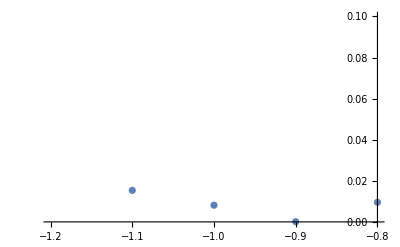

```mathematica
ListPlot[ΔVλ,PlotRange->{{-1.2,-.8},{0,0.1}}]
```

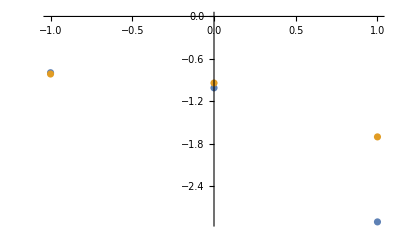

```mathematica
ListPlot[{Δenλ,ΔenSumλ}]
```

#### pure loop w/ vortices

```mathematica
(*Print[];Print["    Pure and with vortices "];Print[];
Do[   Module[{gauge="g4",J,K,Γ,Jmod,Kmod,Γmod,Jv,Kv,Γv,L=Ls[[l]],Nc,h,T,En,EMF,Eλ,EnList={{},{},{}},u0,ES,Δt,hp=Mod[p,Length@hV,1] }, 

 {J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;7]]; 
Nc=L^2;
T=Tmat[L,L];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];
u0=gauge4v[uniformU[-1,L],L];
(* for Pure Kitaev model: *)
Module[ {h0=Norm[h],κ0,κ,χ0,ω0,Hpure,Tpure,Epure,Upure},   
κ0=toKappa[h]; 
κ=N@(Round[10000 κ0]/10000);   
χ0={0,0,0};  (*
ω0=Table[ωGA,2,{r,1,Nc} ];*)
Hpure=Hreal[Kv,κ,toλ[h],u0,L,0, {0,0}] ;   
Tpure=TmatPure[L]; 
Upure=UmatPure[Tpure† . Hpure . Tpure]; 
Epure=Total[Select[Quiet@Eigenvalues[Hpure],#<0&]]/(Nc);

{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];   
χ0=χgauge4v[χ0,L];
dataToFilePure[parameters[[ev,p]],L,acuracy,{0,L,χ0,{{},{}},{{{},{},{}},{{},{},{}}},{Epure} }, gauge,NbName ]; 
(*If[ ev==1, Print["Kappa=",κ,"; Lambda=",toλ[h], "; L=",L,"; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); "]; ];*)
Print[ " eV0=",N[Round[ 1000  parameters[[ev,p]][[10]]/1700 ] /1000] ," x 1700","; Epure=",Epure,"; "];
       ]; 
        ]  , {ev,1,Length[parameters]}, {l,1,Length@Ls}, {p,1,Length[parameters[[1]] ]}  ]   *)
```

#### vortex free

```mathematica
tvf=AbsoluteTime[];Print["Definition timing= ",round[tvf-t0] ]; t0=tvf;
Print[" "];Print["    Starting free loop"];Print[" "];
```

```mathematica
(*Do[ Do[ Module[
{ L=Ls[[l]],Nc,h,En,EnList={{},{},{}},u,u2,U,V,j,Δ1=1,Δ2=1,ES,gap,Δt,ΔtHours,ΔtMin,ΔtSec,kTable,constraintViolation,ΔVseq={},Δseq={},EMF,Esum,η=1,p,Jmat},
 p=Length[hV](pt-1)+ph;
           Nc=L^2;
{Jmat,h}=parameters[[1,p]][[1;;2]];
U=Uguess;V=Vguess;
	Print["Jmat[z] ",MatrixForm[ Jmat[[3]] ],"; L=",L,
"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];
For[j=1,( ( j<(steps))∧(Chop[ Δ1,10^(-8) ]!= 0) ), j++,  


	];



 ];  , {pt,1,Length@tV},  {ph,1,Length@hV}  ],{l,1,Length@Ls}];Print[" "];*)
```

#### vortex free momentum

```mathematica
Do[ Do[ 
Module[{ L=Ls[[l]],Jmat,Nc,h,Λ,T,H,ξ,EnG0,En,EnList={{},{},{}},u,u2,U,V,j,Δ1=1,Δ2=1,ES,gap,Δt,ΔtHours,ΔtMin,ΔtSec,kTable,ΔV,ΔVseq={},Δseq={},EMF,Esum,cMF,η,hp=Mod[p,Length@hV,1],Tk=1/(√2)Tkmom,Umatvec},
η=-1;
{Jmat,h}=parametersMat[[1,p]][[1;;2]];Nc=L^2;
If[ p==1, UG=Uguess; VG=Vguess; ];  (*UG=Uguess; VG=Vguess; *) U=UG; V=VG;   
Print["Jmat=",MatrixForm@Jmat[[3]], "; L=",L,"; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); "];
kTable=toMomentumTable[L];

For[j=1,( ( j<(steps))∧(Chop[ Δ1,10^(-8) ]!= 0) ), j++,  (*If[ (Mod[j,200]==80)∧( Δ1>10^(-6) ), χ=0.6{χGx,χGy,χGz}; Module[{rm=RandomReal[.1,{4,4}]}, ω={ωGA+( rm-Transpose[rm]),ωGB+( rm-Transpose[rm])}] ];*)
(*Print[MatrixForm/@AMFmom[Jmat,U]]; Print[MatrixForm/@BMFmom[Jmat,h, η λeffmom[Jmat,h,V],V] ];*)
Umatvec=UmatVec[Jmat,h,U,V, kTable,Tk,η] ;
u=Chop@Sum [  Module[{k,𝕌,𝕌less,𝕌gtr},k=kTable[[l]];
	(*H0=HmfMomentum[Jmat,h,U,V, k,η];Hr=Tk† . H0 . Tk; Umat=UmatK[Hr];*)𝕌=Tk . Umatvec[[l]];𝕌less=𝕌[[;;,5;;8]]; 𝕌gtr=𝕌[[;;,1;;4]];
(ⅈ/Nc)Conjugate@Chop@{Conjugate[𝕌gtr] . Transpose[𝕌gtr] Exp[ⅈ k . nx]+𝕌less . 𝕌less† Exp[-ⅈ k . nx], Conjugate[𝕌gtr] . Transpose[𝕌gtr] Exp[ⅈ k . ny]+𝕌less . 𝕌less† Exp[-ⅈ k . ny], Conjugate[𝕌gtr] . Transpose[𝕌gtr]+ 𝕌less . 𝕌less†} 
	(*uu=(1/Nc) I TUh . TUh† ; (*uu=(uu-ConjugateTranspose[uu])/2; *) {uu Exp[I k . nx],uu Exp[I k . ny],uu }*)  ],{l,1,Nc} ]; 
U[[1]]=u[[1]][[1;;4,5;;8]] ;U[[2]]=u[[2]][[1;;4,5;;8]];U[[3]]=u[[3]][[1;;4,5;;8]];V[[1]]=u[[3]][[1;;4,1;;4]];V[[2]]=u[[3]][[5;;8,5;;8]];
(*U[[1]]=Table[ u[[1]][[β+4,α]],  {α,1,4},{β,1,4} ];U[[2]]=Table[ u[[2]][[β+4,α]],        {α,1,4},{β,1,4} ];U[[3]]=Table[ u[[3]][[β+4,α]],  {α,1,4},{β,1,4} ];
V[[1]]=Table[ u[[3]][[β,α]]       ,  {α,1,4},{β,1,4} ];V[[2]]=Table[ u[[3]][[β+4,α+4]] ,{α,1,4},{β,1,4} ];*)

ΔV=1/12 Total@Sum[Abs@traceG[V[[σ]]],{σ,1,2}]; ΔVseq={ΔVseq,{j,ΔV}} ;   
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u-u2) ];Δseq={Δseq,{j,Δ1}}  ;   ]; u2=u;  
(* If[j≤3∨j≥steps-2,Print["j=",j,"; Δ=",Δ1,"; Δω=",Δω, ";  ",MatrixForm/@{  χ[[1]],ω[[1]] }];  ] *)                             
Print["j=",j,"; ΔV=",ΔV,"; Δ=",Δ1];
(*Print[ MatrixForm/@Chop[u,.002] ];
Print[ MatrixForm/@Chop[{U[[2]],U[[3]],V[[2]]}] ];*)
(*If[j>=1,  Abort[]  ]*)
                             ];
t1=AbsoluteTime[]; Δt=UnitConvert[ Quantity[t1 -t0, "Seconds" ], "Minutes" ]; t0=t1;
Δseq=Partition[Flatten[Δseq],2]; ΔVseq=Partition[Flatten[ΔVseq],2];
	EMF    = enMFmom[Jmat,U,V,h];
Esum =enSUMmom[Jmat,U,V,h,L];
cMF   =cMFmom[Jmat,U,V];
	dataToFile800[parametersMat[[1,p]],L,acuracy,{j,L,U,V,{0,0},{{EMF},{Esum},{cMF},Δseq,ΔVseq}},"free",NbName]; 
Print["Max Step = ", j,"; Delta=",round@Δ1,(*,"; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Seconds" ]*)"; E=",{EMF,Esum,cMF},
";  p=",p,"/",Length@parametersMat[[1]]];
{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath800[parametersMat[[1,p]],L,acuracy,"free",NbName ]  ];
 ];  

, {p,1,Length[parametersMat[[1]]]}  ],{l,1,Length@Ls}];              Print[" "];
```

Jmat=(0 | 0. | 0
0. | 0 | 0
0 | 0 | -1); L=19; h=(0.,0,0);

j=1; ΔV=8.49435×10^-8; Δ=1

j=2; ΔV=3.32419×10^-8; Δ=2.89894×10^-7

j=3; ΔV=1.30088×10^-8; Δ=1.13447×10^-7

j=4; ΔV=5.09085×10^-9; Δ=4.43961×10^-8

j=5; ΔV=1.99224×10^-9; Δ=1.73739×10^-8

j=6; ΔV=7.7964×10^-10; Δ=6.79905×10^-9

Max Step = 7; Delta=0.; E={-0.787348,-0.787348,-0.787348};  p=1/1

#### vortex free + gradually increase electric field

```mathematica
Module[{Δt}, t0v=AbsoluteTime[];
Δt= UnitConvert[ Quantity[N[t0v-tvf], "Seconds" ], "Minutes" ];   
Print["Free loop timing= ", IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Seconds" ]    ];t0=t0v;
Print[" "] Print[" "];];
Print["    Starting vortex free + electric field loop: "];Print[" "]
```

```mathematica
Do[  Module[
{ L=Ls[[l]],Nc,h,En,EnList={{},{},{}},EMF,Esum,Econst,u0,u1,u2,U,ξ,V,j,Δ1=1,Δ2=1,ES,gap,Δt,ΔtHours,ΔtMin,ΔtSec,kTable,ΔV,ΔVseq={},Δseq={},η=1,p,Jmat,JmatMod,hv,gauge="g0",Jarray,T},
 p=Length[hV](pt-1)+ph;         Nc=L^2; T=Tmat[L,L];
{Jmat,h}=parameters[[1,p]][[1;;2]]; {JmatMod,hv}=parameters[[1,p]][[3;;4]];
Print["Jmat[z] ",MatrixForm[ Jmat[[3]] ],"; L=",L,"; h=(", hV[[ ph,1 ]],",",hV[[ ph,2 ]],",",hV[[ ph,3]],"); "];
	u0=uniformU[-1,L]; (* <-  the 2nd difference : gauge4v *) 	(*{jG,LG,UG,VG,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ];*) 
	V=Table[Vguess,{r,1,Nc}];
	U=Table[Uguess,{r,1,Nc}];
Module[ {h0=Norm[h],κ0,κ,λ=toλ[h],χ0,Hpure,Tpure,Upure,Epure,Kv},   
κ0=toKappa[h]; 
κ=N@(Round[10000 κ0]/10000);   
χ0={0,0,0};  (* ω0=Table[ωGA,2,{r,1,Nc} ];*)
Kv=add4VorticesMaxSpaced[ uniform[Jmat[[3]][[3,3]],L,L],JmatMod[[3]][[3,3]],L];
Hpure=Hreal[Kv,κ,λ,u0,L,0, {0,0}] ;   
Tpure=TmatPure[L];  
Upure=UmatPure[Tpure† . Hpure . Tpure];
Epure=Total[Select[Quiet@Eigenvalues[Hpure],#<0&]]/(Nc);
{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];   
dataToFilePure[parameters[[1,p]],L,acuracy,gauge,{0,L,χ0,{{},{}},{{{},{},{}},{{},{},{}}},{Epure} } ]; 
Print["Pure data saved: "];
Print["Kappa=",κ,"; Lambda=", λ, "; Epure=",Epure,"; "];Print[];
Do[ U[[r,1]][[1,1]]=χ0[[1,r]][[1,1]]; U[[r,2]][[1,1]]=χ0[[2,r]][[1,1]]; U[[r,3]][[1,1]]=χ0[[3,r]][[1,1]]; ,{r,1,Nc}];
  ]; 

Do[ {Jmat,h}=parameters[[ev,p]][[1;;2]];{JmatMod,hv}=parameters[[ev,p]][[3;;4]]; Print[" "];
Jarray=Jarray4v[Table[Jmat,L^2],JmatMod,L];

For[j=1, ( j<steps)∧((j<minSteps)∨(Chop[ Δ1, 10^-acuracy ]!= 0)    ) , j++,   
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u1-u2) ]; Δseq={Δseq,{j,Δ1}};  ΔV=1/(2 Nc) Sum[Abs[traceG[V[[r,σ]]]],{r,1,Nc},{σ,1,2}]; ΔVseq={ΔVseq,{j,ΔV}}    ]; 

Module[{H,u},  H=Hmf[Jarray,h,U,V,L,1] ;u=Umat[T† . H . T];u1=Re@Chop@icc[u,L,T];

EMF=EnMF[ Jarray,h,U,V, L,1];Esum=eigenvaluesEmf[ Jarray,h,U,V, L,1];Econst=constantMF[Jarray,U,V,L];
EnList[[1]]={EnList[[1]],{j,EMF}};    EnList[[2]]={EnList[[2]],{j,Esum}};    EnList[[3]]={EnList[[3]],{j,Econst}};   

Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1;
   n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1]; 
    U[[rz+1,1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];    U[[rz+1,2,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];    U[[rz+1,3,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    V[[rz+1,1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];    V[[rz+1,2,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1] ]];    ]; , {R0,0,16Nc-1}  ];    ]; 

u2=u1;                                                 Print[" j =",j, "/",steps, "; Delta=",round@Δ1, ";  E=", round/@{EMF,Esum,Econst},"; "  ];     
];  
Module[{H,u}, H=Hmf[Jarray,h,U,V,L,1]; u=Umat[T† . H . T]; {U,V,ξ,u1}=BiParallel[u,L,T];   ];  	
Δseq=Partition[Flatten[Δseq],2];
	EnList[[1]]=Partition[Flatten[EnList[[1]]],2];
	EnList[[2]]=Partition[Flatten[EnList[[2]]],2];
	EnList[[3]]=Partition[Flatten[EnList[[3]]],2]; 
	ΔVseq=Partition[Flatten[ΔVseq],2]; 
	dataToFile[parameters[[ev,p]],L,acuracy,{j,L,U,V,ξ,{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,ΔVseq}},gauge,NbName];     

Print[ "ev=",ev ,"/", Length@eVs"; j MAX=",j, "/",steps, "; Delta=",Δ1, "; "   ]; , {ev,1,Length[parameters]} ];



 ];  , {pt,1,Length@tV},  {ph,1,Length@hV}  ,{l,1,Length@Ls}];Print[" "];
```

```mathematica
minSteps=3;
Do[   
Module[{χG,ωG,jG,LG,EnG ,gauge="g0"},   (* <-  the 1st difference : g0 <-> g4 *)
Module[{ J,K,Γ,Jmod,Kmod,Γmod,Jv,Kv,Γv,L=Ls[[l]],Nc,h ,Λ,T,En,EMF,Esum,Eλ,EnList={{},{},{}},ξG,Δseq={},Δωseq={},Δω,u2=0,u1,u0,χ={0,0,0},ω={0,0},ξ={0,0},j,Δ1=1,Δ2=2.56,ES,gap,Δt,hp=Mod[p,Length@hV,1] }, 
{J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[1,p]][[1;;7]]; 
Nc=L^2;
ω=Table[ωGA,2,{r,1,Nc} ];
T=Tmat[L,L];
Kv=uniform[K,L,L];

u0=uniformU[-1,L]; (* <-  the 2nd difference : gauge4v *)

{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ]; 
(*ωG=symω[ωG];*)
ω[[1]]=Table[ωG[[1]],{r,1,Nc} ];
ω[[2]]=Table[ωG[[2]],{r,1,Nc} ];
χ[[1]]=Table[χG[[1]],{r,1,Nc} ];
χ[[2]]=Table[χG[[2]],{r,1,Nc} ];
χ[[3]]=Table[χG[[3]],{r,1,Nc} ];

(* Print[" for Pure Kitaev model: " ];*)
Module[ {h0=Norm[h],κ0,κ,λ=toλ[h],χ0,Hpure,Tpure,Upure,Epure},   
κ0=(*(h0/Sqrt[3])^3/(0.262)^2*) toKappa[h]; 
κ=N@(Round[10000 κ0]/10000);   
χ0={0,0,0};  (*
ω0=Table[ωGA,2,{r,1,Nc} ];*)
Hpure=Hreal[Kv,κ,λ,u0,L,0, {0,0}] ;   
Tpure=TmatPure[L];  
Upure=UmatPure[Tpure† . Hpure . Tpure];
Epure=Total[Select[Quiet@Eigenvalues[Hpure],#<0&]]/(Nc);
{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];   
dataToFilePure[parameters[[1,p]],L,acuracy,gauge,{0,L,χ0,{{},{}},{{{},{},{}},{{},{},{}}},{Epure} } ]; 
Print["Pure data saved: "];
Print["Kappa=",κ,"; Lambda=", λ, "; Epure=",Epure,"; "];Print[];
Do[ χ[[1,r]][[1,1]]=χ0[[1,r]][[1,1]]; χ[[2,r]][[1,1]]=χ0[[2,r]][[1,1]]; χ[[3,r]][[1,1]]=χ0[[3,r]][[1,1]]; ,{r,1,Nc}];
  ]; 

(*χ=χgauge4v[χ,L];*)   (* <-  the 3rd difference :  χgauge4v *)

 Do[ {J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;7]]; Print[" "];
Print["J=",J, "; K=",K, "; G=",Γ,"; Jmod=",Jmod, "; Kmod=",Kmod, "; Gmod=",Γmod, "; L=",L, "; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); eV=",N[Round[1000 eVs[[ev]]/1700]/1000]"; "];Print[" "];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];

For[j=1, ( j<steps)∧((j<minSteps)∨(Chop[ Δ1, 10^-acuracy ]!= 0)    ) , j++,   
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u1-u2) ]; Δseq={Δseq,{j,Δ1}};  Δω=1/(2 Nc) Sum[Abs[ω[[σ,r,2,1]]+ω[[σ,r,3,4]]],{r,1,Nc},{σ,1,2}]; Δωseq={Δωseq,{j,Δω}}    ]; 

Module[{H,u,TUh,Heff,λ1,λ2,loaddata},
If[j<=1, loaddata=loadDataTry[toPath[parameters[[ev,p]],L,acuracy,gauge,NbName]  ];
If[!(loaddata===$Failed),{j,L,χ,ω,ξ,{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,Δωseq}}=loaddata]];

Heff=HeffList[Jv,Kv,Γv,h,ω];(*  λ1=1/2 Heff;λ2=1/2 Heff;  *)
λ1=λ1List[Heff,ω];λ2=λ2List[Heff,ω]; 
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 
u=Umat[T† . H . T];
u1=Re@Chop@icc[u,L,T];

	EMF=EnMF0[Jv,Kv,Γv,h,χ,ω,L,L];                                        (* <- EnMF0 ?  *)
	Esum=Total[Select[Quiet@Eigenvalues[H],#<0&]]/(2Nc);
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,Esum}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};   
Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1;
   n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1]; 
    χ[[1,rz+1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1] ]];
    ]; , {R0,0,16Nc-1}  ];    
]; 
u2=u1;        
Print[" j =",j, "/",steps, "; Delta=",roundΔ@Δ1, ";  E=", N[Round[1000000(#)]/1000000]&@{EMF,Esum,EMF+Eλ},"; "  ];     
         ];  
Module[{H,u,Heff,λ1,λ2},Heff=HeffList[Jv,Kv,Γv,h,ω]; (*
λ1=1/2 Heff;λ2=1/2 Heff;*)
λ1=λ1List[Heff,ω];λ2=λ2List[Heff,ω]; 
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 
    u=Umat[T† . H . T];
	{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],ξ[[1]],ξ[[2]],u1}=BiParallel[u,L,T];

	EMF=EnMF0[Jv,Kv,Γv,h,χ,ω,L,L];                                        (* <- EnMF0 ?  *)
	Esum=Total[Select[Quiet@Eigenvalues[H],#<0&]]/(2Nc);
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,Esum}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};      

];  	Δseq=Partition[Flatten[Δseq],2];
	EnList[[1]]=Partition[Flatten[EnList[[1]]],2];
	EnList[[2]]=Partition[Flatten[EnList[[2]]],2];
	EnList[[3]]=Partition[Flatten[EnList[[3]]],2]; 
	Δωseq=Partition[Flatten[Δωseq],2]; 
	dataToFile[parameters[[ev,p]],L,acuracy,{j,L,χ,ω,ξ,{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,Δωseq}},gauge,NbName];     
Print[ "ev=",ev ,"/", Length@eVs"; j MAX=",j, "/",steps, "; Delta=",Δ1, "; "   ];
, {ev,1,Length[parameters]} ]   ;

	t1=AbsoluteTime[];Δt= UnitConvert[ Quantity[N[t1 -t0], "Seconds" ], "Hours" ];t0=t1;Print[" "];
	Print[ "p=",p,"/",Length@parameters[[1]], "; l=",l, "/",Length@Ls, "; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ]   ]
  ];
]  , {l,1,Length@Ls}, {p,1,Length[parameters[[1]] ]}  ];
```

#### four vortex + gradually increase electric field

```mathematica
Module[{Δt},t4v=AbsoluteTime[];Δt= UnitConvert[ Quantity[N[t4v-t0v], "Seconds" ], "Hours" ];
ΔtHours=IntegerPart[Δt];
ΔtMin=IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ];
ΔtSec=IntegerPart@UnitConvert[FractionalPart@UnitConvert[FractionalPart[Δt], "Minutes" ], "Seconds" ];
Print[ "Free loop + electric field timing= ",ToString@ΔtHours," : ",ToString@ΔtMin," : ",ToString@ΔtSec    ];
t0=t4v;Print[" "] Print[" "];
];
Print["    Starting four vortex + electric field loop: "];Print[" "]
```

```mathematica
(*
minSteps=5;
Do[   Module[{χG,ωG,jG,LG,EnG ,gauge="g4"},   (* <-  the 1st difference : g0 <-> g4 *)
Module[{ J,K,Γ,Jmod,Kmod,Γmod,Jv,Kv,Γv,L=Ls[[l]],Nc,h ,Λ,T,En,EMF,Eλ,EnList={{},{},{}},ξG,Δseq={},Δωseq={},Δω,u2,u1,u0,χ={0,0,0},ω={0,0},ξ={0,0},j,Δ1=1,Δ2=2.56,ES,gap,Δt,hp=Mod[p,Length@hV,1] }, 
{J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[1,p]][[1;;7]];  
Nc=L^2;
ω=Table[ωGA,2,{r,1,Nc} ];
T=Tmat[L,L];
Kv=uniform[K,L,L];

u0=gauge4v[uniformU[-1,L],L]; (* <-  the 2nd difference : gauge4v *)

{jG,LG,χG,ωG,ξG,EnG}= loadData[toPath[parameters[[1,p]],L,acuracy,"free",NbName ]  ]; 
(*ωG=symω[ωG];*)
ω[[1]]=Table[ωG[[1]],{r,1,Nc} ];
ω[[2]]=Table[ωG[[2]],{r,1,Nc} ];
χ[[1]]=Table[χG[[1]],{r,1,Nc} ];
χ[[2]]=Table[χG[[2]],{r,1,Nc} ];
χ[[3]]=Table[χG[[3]],{r,1,Nc} ];

(* Print[" for Pure Kitaev model: " ];*)
Module[ {h0=Norm[h],κ0,κ,χ0,Hpure,Tpure,Upure},   
κ0=(*(h0/Sqrt[3])^3/(0.262)^2*) toKappa[h]; 
κ=N@(Round[10000 κ0]/10000);   
χ0={0,0,0};  (*
ω0=Table[ωGA,2,{r,1,Nc} ];*)
Hpure=Hreal[Kv,κ,toλ[h],u0,L,0, {0,0}] ;   
Tpure=TmatPure[L];  
Upure=UmatPure[Tpure† . Hpure . Tpure];
Epure=Total[Select[Quiet@Eigenvalues[Hpure],#<0&]]/(Nc);
{χ0[[1]],χ0[[2]],χ0[[3]]}=toMFparametersPure[Upure,u0,L,0];   
dataToFilePure[parameters[[1,p]],L,acuracy,gauge,{0,L,χ0,{{},{}},{{{},{},{}},{{},{},{}}},{Epure} } ]; 
Print["Pure data saved: "];
Print["Kappa=",κ," Lambda=", λ ,"; Epure=",Epure,"; "];Print[];
Do[ χ[[1,r]][[1,1]]=χ0[[1,r]][[1,1]]; χ[[2,r]][[1,1]]=χ0[[2,r]][[1,1]]; χ[[3,r]][[1,1]]=χ0[[3,r]][[1,1]]; ,{r,1,Nc}];
  ]; 

χ=χgauge4v[χ,L];   (* <-  the 3rd difference :  χgauge4v *)

 Do[ {J,K,Γ,h,Jmod,Kmod,Γmod}=parameters[[ev,p]][[1;;7]]; Print[" "];
Print["J=",J, "; K=",K, "; G=",Γ,"; Jmod=",Jmod, "; Kmod=",Kmod, "; Gmod=",Γmod, "; L=",L, "; h=(", hV[[ hp,1 ]],",",hV[[ hp,2 ]],",",hV[[ hp,3]],"); eV=",N[Round[1000 eVs[[ev]]/1700]/1000]"; "];Print[" "];
Kv=uniform[K,L,L];Kv=add4VorticesMaxSpaced[ Kv,Kmod,L];
Jv=uniform[J,L,L];Jv=add4VorticesMaxSpaced[ Jv,Jmod,L];
Γv=uniform[Γ,L,L];Γv=add4VorticesMaxSpaced[ Γv,Γmod,L];
For[j=1, ( j<steps)∧((j<minSteps)∨(Chop[ Δ1, 10^-acuracy ]!= 0)    ) , j++,   

Module[{H,u,TUh,Heff,λ1,λ2},Heff=HeffList[Jv,Kv,Γv,h,ω];
λ1=1/2 Heff;λ2=1/2 Heff;
(*λ1=λ1List[Heff,ω];λ2=λ2List[Heff,ω]; *)
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 
u=Umat[T† . H . T];
u1=Re@Chop@icc[u,L,T];

	EMF=EnMF0[Jv,Kv,Γv,h,χ,ω,L,L];                                        (* <- EnMF0 ?  *)
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,0}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};   

Do[ Module[{m,n,α,β,rz,rx,ry,Io}, rz=⌊R0/16⌋;β=⌊1+(R0-16rz)/4⌋;α=R0-16rz-4(β-1)+1;
   n=⌊rz/L⌋;m=rz-n L;rx=Mod[m+1,L]+n L;ry=m+Mod[n+1,L] L;Io=Mod[α+8rz,8Nc,1]; 
    χ[[1,rz+1,α,β]]=u1[[Mod[β+4+8rx,8Nc,1],Io]];
    χ[[2,rz+1,α,β]]=u1[[Mod[β+4+8ry,8Nc,1],Io]];
    χ[[3,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Io]];
    ω[[1,rz+1,α,β]]=u1[[Mod[β+8rz,8Nc,1],Io]];
    ω[[2,rz+1,α,β]]=u1[[Mod[β+4+8rz,8Nc,1],Mod[Io+4,8Nc,1] ]];
    ]; , {R0,0,16Nc-1}  ];     
]; 
If[j>=2,Δ2=Δ1; Δ1=Max[ Abs@(u1-u2) ]; Δseq={Δseq,{j,Δ1}};  Δω=1/(2 Nc) Sum[Abs[ω[[σ,r,2,1]]+ω[[σ,r,3,4]]],{r,1,Nc},{σ,1,2}]; Δωseq={Δωseq,{j,Δω}}    ]; 
u2=u1;        
Print[" j =",j, "/",steps, "; Delta=",roundΔ@Δ1,  ";  E=", N[Round[1000000(EMF)]/1000000],"; "  ];     
         ];  
Module[{H,u,Heff,λ1,λ2},
Heff=HeffList[Jv,Kv,Γv,h,ω]; 
λ1=(0.46)Heff;λ2=(0.46)Heff;
(*λ1=λ1List[Heff,ω];λ2=λ2List[Heff,ω]; *)
H=HMF[Jv,Kv,Γv,h,χ,ω,L,L,λ1,λ2,Heff]; 
    u=Umat[T† . H . T];
	{χ[[1]],χ[[2]],χ[[3]],ω[[1]],ω[[2]],ξ[[1]],ξ[[2]],u1}=BiParallel[u,L,T]; 
	EMF=EnMF0[Jv,Kv,Γv,h,χ,ω,L,L]; 
	Eλ=EnLagMF[Jv,Kv,Γv,h,χ,ω,L,L];
	EnList[[1]]={EnList[[1]],{j,EMF}};
    EnList[[2]]={EnList[[2]],{j,0}};
    EnList[[3]]={EnList[[3]],{j,EMF+Eλ}};           
];  	Δseq=Partition[Flatten[Δseq],2];
	EnList[[1]]=Partition[Flatten[EnList[[1]]],2];
	EnList[[2]]=Partition[Flatten[EnList[[2]]],2];
	EnList[[3]]=Partition[Flatten[EnList[[3]]],2]; 
	Δωseq=Partition[Flatten[Δωseq],2]; 
	dataToFile[parameters[[ev,p]],L,acuracy,{j,L,χ,ω,ξ,{EnList[[1]],EnList[[2]],EnList[[3]],Δseq,Δωseq}},gauge,NbName];     
	
Print[ "ev=",ev ,"/", Length@eVs"; j MAX=",j, "/",steps, "; Delta=",Δ1, "; "   ], {ev,1,Length[parameters]} ];

	t1=AbsoluteTime[];Δt= UnitConvert[ Quantity[N[t1 -t0], "Seconds" ], "Hours" ];t0=t1; Print[" "];
	Print[ "p=",p,"/",Length@parameters[[1]], "; l=",l, "/",Length@Ls, "; Δt = ",IntegerPart[Δt],IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ]   ]

  ];
]  , {l,1,Length@Ls}, {p,1,Length[parameters[[1]] ]}  ]          
*)
```

```mathematica
Module[{Δt},t1=AbsoluteTime[];Δt= UnitConvert[ Quantity[N[t1-t4v], "Seconds" ], "Hours" ];
ΔtHours=IntegerPart[Δt];
ΔtMin=IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ];
ΔtSec=IntegerPart@UnitConvert[FractionalPart@UnitConvert[FractionalPart[Δt], "Minutes" ], "Seconds" ];
Print[ "4 vortices loop timing Δt = ",ToString@ΔtHours," : ",ToString@ΔtMin," : ",ToString@ΔtSec    ] 
];
```

```mathematica
(*Module[{Δt},t1=AbsoluteTime[];Δt= UnitConvert[ Quantity[N[t1-t4v], "Seconds" ], "Hours" ];
ΔtHours=IntegerPart[Δt];
ΔtMin=IntegerPart@UnitConvert[FractionalPart[Δt], "Minutes" ];
ΔtSec=IntegerPart@UnitConvert[FractionalPart@UnitConvert[FractionalPart[Δt], "Minutes" ], "Seconds" ];
Print[ "4 vortices loop timing Δt = ",ToString@ΔtHours," : ",ToString@ΔtMin," : ",ToString@ΔtSec    ] ];*)
```

## To do:

× Change W -> V                                                                                              done
× define mf energy   (via <> and eigenvalue)                                done
×     test  it for pure Kitaev h=0                                                                  done
× Wilson loop  ( change order r and σ )                                                done
× function Jmicro[t] output Jmat coupling for each t                  done
× Change def parameters  (define DM as function of eV)             done
× Define DM interaction as uniform 0 + 4v
× Rewrite code for vortex free  (for 4v  then copy it making the trivial changes)